```mathematica
Quit[];
```

```mathematica
ClearAll[dir];
dir=If[DirectoryQ[#],#,CreateDirectory[#]]&@FileNameJoin[{NotebookDirectory[],"Int"}]
```

/home/bwu/Documents/pp/v2/ppv2/Int

## J2

```mathematica
Protect[ρ,η,k,b,x1,x2,x3,x4,I1a,I2a,I3a,I0a,SP];
```

```mathematica
ClearAll[I1NHuge,I1NLarge,I1NSmall,I2NHuge,I2NLarge,I2NSmall];
I1NHuge=<<(FileNameJoin[{dir,"I1NHuge"}]);
I1NLarge=<<(FileNameJoin[{dir,"I1NLarge"}]);
I1NSmall=<<(FileNameJoin[{dir,"I1NSmall"}]);
I2NHuge=<<(FileNameJoin[{dir,"I2NHuge"}]);
I2NLarge=<<(FileNameJoin[{dir,"I2NLarge"}]);
I2NSmall=<<(FileNameJoin[{dir,"I2NSmall"}]);
```

```mathematica
ClearAll[I1NLargeFun,I1NSmallFun,I2NLargeFun,I2NSmallFun];
I1NHugeFun=Interpolation[I1NHuge,InterpolationOrder->3,Method->"Hermite"];
I1NLargeFun=Interpolation[I1NLarge,InterpolationOrder->3,Method->"Hermite"];
I1NSmallFun=Interpolation[I1NSmall,InterpolationOrder->3,Method->"Hermite"];
I2NHugeFun=Interpolation[I2NHuge,InterpolationOrder->3,Method->"Hermite"];
I2NLargeFun=Interpolation[I2NLarge,InterpolationOrder->3,Method->"Hermite"];
I2NSmallFun=Interpolation[I2NSmall,InterpolationOrder->3,Method->"Hermite"];
```

Note the argument in I1NSmall and I2NSmall is ρ and Log[10,η]

```mathematica
ClearAll[I0Fun,I1Fun,I2Fun,I3Fun];
I0Fun=Compile[{{ρ,_Real},{η,_Real}},Exp[ⅈ ρ η]/(4π)(CosIntegral[Abs[ρ]η]-ⅈ SinIntegral[ρ η]+Log[η/(4Abs[ρ])]+EulerGamma),CompilationTarget->"WVM"];
I1Fun[ρ_,η_]:=Which[η<1/10,I1NSmallFun[ρ,Log[10,η]],η≥ 1/10&&η≤50,I1NLargeFun[ρ,η],True,I1NHugeFun[ρ,η]];
I2Fun[ρ_,η_]:=Which[η<1/10,I2NSmallFun[ρ,Log[10,η]],η≥1/10&&η≤50,I2NLargeFun[ρ,η],True,I2NHugeFun[ρ,η]];
I3Fun=Compile[{{ρ,_Real},{η,_Real}},-ⅈ/(4π)(1-Exp[ⅈ ρ η])Log[η]/(ρ η)];
```

```mathematica
ClearAll[J2Compile];
J2Compile=Compile[{{kx,_Real},{ky,_Real},{bx,_Real},{by,_Real},{x1x,_Real},{x1y,_Real},{x2x,_Real},{x2y,_Real},{x3x,_Real},{x3y,_Real},{x4x,_Real},{x4y,_Real}},

res=Module[{NSP,CoefList,I01b13,I01b23,I01b14,I01b24,I23b13,I23b23,I23b14,I23b24,IntList},
NSP[1]=bx^2+by^2;
NSP[2]=bx*x1x+by*x1y;
NSP[3]=bx*x2x+by*x2y;
NSP[4]=bx*x3x+by*x3y;
NSP[5]=bx*x4x+by*x4y;
NSP[6]=bx*kx+by*ky;
NSP[7]=kx^2+ky^2;
NSP[8]=kx*x1x+ky*x1y;
NSP[9]=kx*x2x+ky*x2y;
NSP[10]=kx*x3x+ky*x3y;
NSP[11]=kx*x4x+ky*x4y;
NSP[12]=x1x^2+x1y^2;
NSP[13]=x1x*x2x+x1y*x2y;
NSP[14]=x1x*x3x+x1y*x3y;
NSP[15]=x1x*x4x+x1y*x4y;
NSP[16]=x2x^2+x2y^2;
NSP[17]=x2x*x3x+x2y*x3y;
NSP[18]=x2x*x4x+x2y*x4y;
NSP[19]=x3x^2+x3y^2;
NSP[20]=x3x*x4x+x3y*x4y;
NSP[21]=x4x^2+x4y^2;

(*Print[Table[NSP[ii],{ii,1,21}]];*)

CoefList={{1,-E^((-I)*(NSP[8]-NSP[9])),-1,E^((-I)*(NSP[8]-NSP[9])),-NSP[6]-NSP[8]+NSP[10],(NSP[6]+NSP[9]-NSP[10])/E^(I*(NSP[8]-NSP[9])),NSP[6]+NSP[8]-NSP[11],-((NSP[6]+NSP[9]-NSP[11])/E^(I*(NSP[8]-NSP[9])))},{-E^(I*(NSP[8]-NSP[9])),1,E^(I*(NSP[8]-NSP[9])),-1,E^(I*(NSP[8]-NSP[9]))*(NSP[6]+NSP[8]-NSP[10]),-NSP[6]-NSP[9]+NSP[10],-(E^(I*(NSP[8]-NSP[9]))*(NSP[6]+NSP[8]-NSP[11])),NSP[6]+NSP[9]-NSP[11]},{-1,E^((-I)*(NSP[8]-NSP[9])),1,-E^((-I)*(NSP[8]-NSP[9])),NSP[6]+NSP[8]-NSP[10],-((NSP[6]+NSP[9]-NSP[10])/E^(I*(NSP[8]-NSP[9]))),-NSP[6]-NSP[8]+NSP[11],(NSP[6]+NSP[9]-NSP[11])/E^(I*(NSP[8]-NSP[9]))},{E^(I*(NSP[8]-NSP[9])),-1,-E^(I*(NSP[8]-NSP[9])),1,-(E^(I*(NSP[8]-NSP[9]))*(NSP[6]+NSP[8]-NSP[10])),NSP[6]+NSP[9]-NSP[10],E^(I*(NSP[8]-NSP[9]))*(NSP[6]+NSP[8]-NSP[11]),-NSP[6]-NSP[9]+NSP[11]},{-NSP[6]-NSP[8]+NSP[10],(NSP[6]+NSP[8]-NSP[10])/E^(I*(NSP[8]-NSP[9])),NSP[6]+NSP[8]-NSP[10],-((NSP[6]+NSP[8]-NSP[10])/E^(I*(NSP[8]-NSP[9]))),NSP[7]*(NSP[1]+2*NSP[2]-2*NSP[4]+NSP[12]-2*NSP[14]+NSP[19]),-((NSP[7]*(NSP[1]+NSP[2]+NSP[3]-2*NSP[4]+NSP[13]-NSP[14]-NSP[17]+NSP[19]))/E^(I*(NSP[8]-NSP[9]))),NSP[7]*(-NSP[1]-2*NSP[2]+NSP[4]+NSP[5]-NSP[12]+NSP[14]+NSP[15]-NSP[20]),(NSP[7]*(NSP[1]+NSP[2]+NSP[3]-NSP[4]-NSP[5]+NSP[13]-NSP[15]-NSP[17]+NSP[20]))/E^(I*(NSP[8]-NSP[9]))},{E^(I*(NSP[8]-NSP[9]))*(NSP[6]+NSP[9]-NSP[10]),-NSP[6]-NSP[9]+NSP[10],-(E^(I*(NSP[8]-NSP[9]))*(NSP[6]+NSP[9]-NSP[10])),NSP[6]+NSP[9]-NSP[10],-(E^(I*(NSP[8]-NSP[9]))*NSP[7]*(NSP[1]+NSP[2]+NSP[3]-2*NSP[4]+NSP[13]-NSP[14]-NSP[17]+NSP[19])),NSP[7]*(NSP[1]+2*NSP[3]-2*NSP[4]+NSP[16]-2*NSP[17]+NSP[19]),E^(I*(NSP[8]-NSP[9]))*NSP[7]*(NSP[1]+NSP[2]+NSP[3]-NSP[4]-NSP[5]+NSP[13]-NSP[14]-NSP[18]+NSP[20]),NSP[7]*(-NSP[1]-2*NSP[3]+NSP[4]+NSP[5]-NSP[16]+NSP[17]+NSP[18]-NSP[20])},{NSP[6]+NSP[8]-NSP[11],-((NSP[6]+NSP[8]-NSP[11])/E^(I*(NSP[8]-NSP[9]))),-NSP[6]-NSP[8]+NSP[11],(NSP[6]+NSP[8]-NSP[11])/E^(I*(NSP[8]-NSP[9])),NSP[7]*(-NSP[1]-2*NSP[2]+NSP[4]+NSP[5]-NSP[12]+NSP[14]+NSP[15]-NSP[20]),(NSP[7]*(NSP[1]+NSP[2]+NSP[3]-NSP[4]-NSP[5]+NSP[13]-NSP[14]-NSP[18]+NSP[20]))/E^(I*(NSP[8]-NSP[9])),NSP[7]*(NSP[1]+2*NSP[2]-2*NSP[5]+NSP[12]-2*NSP[15]+NSP[21]),-((NSP[7]*(NSP[1]+NSP[2]+NSP[3]-2*NSP[5]+NSP[13]-NSP[15]-NSP[18]+NSP[21]))/E^(I*(NSP[8]-NSP[9])))},{-(E^(I*(NSP[8]-NSP[9]))*(NSP[6]+NSP[9]-NSP[11])),NSP[6]+NSP[9]-NSP[11],E^(I*(NSP[8]-NSP[9]))*(NSP[6]+NSP[9]-NSP[11]),-NSP[6]-NSP[9]+NSP[11],E^(I*(NSP[8]-NSP[9]))*NSP[7]*(NSP[1]+NSP[2]+NSP[3]-NSP[4]-NSP[5]+NSP[13]-NSP[15]-NSP[17]+NSP[20]),NSP[7]*(-NSP[1]-2*NSP[3]+NSP[4]+NSP[5]-NSP[16]+NSP[17]+NSP[18]-NSP[20]),-(E^(I*(NSP[8]-NSP[9]))*NSP[7]*(NSP[1]+NSP[2]+NSP[3]-2*NSP[5]+NSP[13]-NSP[15]-NSP[18]+NSP[21])),NSP[7]*(NSP[1]+2*NSP[3]-2*NSP[5]+NSP[16]-2*NSP[18]+NSP[21])}};

Module[{eta,rho},
eta=(((bx+x1x-x3x)(bx+x1x-x3x)+(by+x1y-x3y)(by+x1y-x3y))NSP[7])^(1/2);
rho=(kx(bx+x1x-x3x)+ky(by+x1y-x3y))/eta;
I01b13=I0Fun[rho,eta]+I1Fun[rho,eta];
I23b13=I2Fun[rho,eta]+I3Fun[rho,eta];
];

Module[{eta,rho},
eta=(((bx+x2x-x3x)(bx+x2x-x3x)+(by+x2y-x3y)(by+x2y-x3y))NSP[7])^(1/2);
rho=(kx(bx+x2x-x3x)+ky(by+x2y-x3y))/eta;
I01b23=I0Fun[rho,eta]+I1Fun[rho,eta];
I23b23=I2Fun[rho,eta]+I3Fun[rho,eta];
];

Module[{eta,rho},
eta=(((bx+x1x-x4x)(bx+x1x-x4x)+(by+x1y-x4y)(by+x1y-x4y))NSP[7])^(1/2);
rho=(kx(bx+x1x-x4x)+ky(by+x1y-x4y))/eta;
I01b14=I0Fun[rho,eta]+I1Fun[rho,eta];
I23b14=I2Fun[rho,eta]+I3Fun[rho,eta];
];

Module[{eta,rho},
eta=(((bx+x2x-x4x)(bx+x2x-x4x)+(by+x2y-x4y)(by+x2y-x4y))NSP[7])^(1/2);
rho=(kx(bx+x2x-x4x)+ky(by+x2y-x4y))/eta;
I01b24=I0Fun[rho,eta]+I1Fun[rho,eta];
I23b24=I2Fun[rho,eta]+I3Fun[rho,eta];
];


IntList={I01b13,I01b23,I01b14,I01b24,-ⅈ*I23b13,-ⅈ*I23b23,-ⅈ*I23b14,-ⅈ*I23b24};

(IntList.CoefList.ConjugateTranspose[{IntList}])[[1]]//Re
],
{{res,_Real}},CompilationTarget->"WVM"
];



ClearAll[J2CompileN];
J2CompileN[kx_?NumericQ,ky_?NumericQ,bx_?NumericQ,by_?NumericQ,x1x_?NumericQ,x1y_?NumericQ,x2x_?NumericQ,x2y_?NumericQ,x3x_?NumericQ,x3y_?NumericQ,x4x_?NumericQ,x4y_?NumericQ]:=J2Compile[kx,ky,bx,by,x1x,x1y,x2x,x2y,x3x,x3y,x4x,x4y];
```

## Analytic J2 (from oneGluon_dipole.nb)

```mathematica
F1s[{bx_,by_},{x1_,y1_},{x2_,y2_},{x3_,y3_},{x4_,y4_}]:=1/(4 π)(ⅇ^(-ⅈ (kx x1+ky y1)) (-Log[(bx+x1-x3)^2+(by+y1-y3)^2]+Log[(bx+x1-x4)^2+(by+y1-y4)^2])+ⅇ^(-ⅈ (kx x2+ky y2)) (Log[(bx+x2-x3)^2+(by+y2-y3)^2]-Log[(bx+x2-x4)^2+(by+y2-y4)^2]))
F2s[{bx_,by_},{x1_,y1_},{x2_,y2_},{x3_,y3_},{x4_,y4_},{kx_,ky_}]:=(1/(4 (kx^2+ky^2) π)(ⅇ^(-ⅈ (kx x1+ky y1)) (-(1+ⅇ^(ⅈ (kx (bx+x1-x3)+ky (by+y1-y3)))) (EulerGamma+Log[π]+Log[(bx+x1-x3)^2+(by+y1-y3)^2]+2 Log[μ])+(1+ⅇ^(ⅈ (kx (bx+x1-x4)+ky (by+y1-y4)))) (EulerGamma+Log[π]+Log[(bx+x1-x4)^2+(by+y1-y4)^2]+2 Log[μ])+ⅇ^(1/2 (ⅈ kx (bx+x1-x3)+ⅈ ky (by+y1-y3)-Abs[ky (bx+x1-x3)-kx (by+y1-y3)])) (CosIntegral[1/2 (kx (bx+x1-x3)+ky (by+y1-y3)-ⅈ Abs[ky (bx+x1-x3)-kx (by+y1-y3)])]+CosIntegral[1/2 (kx (bx+x1-x3)+ky (by+y1-y3)+ⅈ Abs[ky (bx+x1-x3)-kx (by+y1-y3)])]-SinhIntegral[1/2 (ⅈ kx (bx+x1-x3)+ⅈ ky (by+y1-y3)-Abs[ky (bx+x1-x3)-kx (by+y1-y3)])]+SinhIntegral[1/2 (ⅈ kx (bx+x1-x3)+ⅈ ky (by+y1-y3)+Abs[ky (bx+x1-x3)-kx (by+y1-y3)])]+ⅇ^Abs[ky (bx+x1-x3)-kx (by+y1-y3)] (CosIntegral[1/2 (-kx (bx+x1-x3)-ky (by+y1-y3)-ⅈ Abs[ky (bx+x1-x3)-kx (by+y1-y3)])]+CosIntegral[1/2 ⅈ (ⅈ kx (bx+x1-x3)+ⅈ ky (by+y1-y3)+Abs[ky (bx+x1-x3)-kx (by+y1-y3)])]-SinhIntegral[1/2 (ⅈ kx (bx+x1-x3)+ⅈ ky (by+y1-y3)+Abs[ky (bx+x1-x3)-kx (by+y1-y3)])]+ⅈ SinIntegral[1/2 (kx (bx+x1-x3)+ky (by+y1-y3)+ⅈ Abs[ky (bx+x1-x3)-kx (by+y1-y3)])]))-ⅇ^(1/2 (ⅈ kx (bx+x1-x4)+ⅈ ky (by+y1-y4)-Abs[ky (bx+x1-x4)-kx (by+y1-y4)])) (CosIntegral[1/2 (kx (bx+x1-x4)+ky (by+y1-y4)-ⅈ Abs[ky (bx+x1-x4)-kx (by+y1-y4)])]+CosIntegral[1/2 (kx (bx+x1-x4)+ky (by+y1-y4)+ⅈ Abs[ky (bx+x1-x4)-kx (by+y1-y4)])]-SinhIntegral[1/2 (ⅈ kx (bx+x1-x4)+ⅈ ky (by+y1-y4)-Abs[ky (bx+x1-x4)-kx (by+y1-y4)])]+SinhIntegral[1/2 (ⅈ kx (bx+x1-x4)+ⅈ ky (by+y1-y4)+Abs[ky (bx+x1-x4)-kx (by+y1-y4)])]+ⅇ^Abs[ky (bx+x1-x4)-kx (by+y1-y4)] (CosIntegral[1/2 (-kx (bx+x1-x4)-ky (by+y1-y4)-ⅈ Abs[ky (bx+x1-x4)-kx (by+y1-y4)])]+CosIntegral[1/2 ⅈ (ⅈ kx (bx+x1-x4)+ⅈ ky (by+y1-y4)+Abs[ky (bx+x1-x4)-kx (by+y1-y4)])]-SinhIntegral[1/2 (ⅈ kx (bx+x1-x4)+ⅈ ky (by+y1-y4)+Abs[ky (bx+x1-x4)-kx (by+y1-y4)])]+ⅈ SinIntegral[1/2 (kx (bx+x1-x4)+ky (by+y1-y4)+ⅈ Abs[ky (bx+x1-x4)-kx (by+y1-y4)])])))+ⅇ^(-ⅈ (kx x2+ky y2)) ((1+ⅇ^(ⅈ (kx (bx+x2-x3)+ky (by+y2-y3)))) (EulerGamma+Log[π]+Log[(bx+x2-x3)^2+(by+y2-y3)^2]+2 Log[μ])-(1+ⅇ^(ⅈ (kx (bx+x2-x4)+ky (by+y2-y4)))) (EulerGamma+Log[π]+Log[(bx+x2-x4)^2+(by+y2-y4)^2]+2 Log[μ])-ⅇ^(1/2 (ⅈ kx (bx+x2-x3)+ⅈ ky (by+y2-y3)-Abs[ky (bx+x2-x3)-kx (by+y2-y3)])) (CosIntegral[1/2 (kx (bx+x2-x3)+ky (by+y2-y3)-ⅈ Abs[ky (bx+x2-x3)-kx (by+y2-y3)])]+CosIntegral[1/2 (kx (bx+x2-x3)+ky (by+y2-y3)+ⅈ Abs[ky (bx+x2-x3)-kx (by+y2-y3)])]-SinhIntegral[1/2 (ⅈ kx (bx+x2-x3)+ⅈ ky (by+y2-y3)-Abs[ky (bx+x2-x3)-kx (by+y2-y3)])]+SinhIntegral[1/2 (ⅈ kx (bx+x2-x3)+ⅈ ky (by+y2-y3)+Abs[ky (bx+x2-x3)-kx (by+y2-y3)])]+ⅇ^Abs[ky (bx+x2-x3)-kx (by+y2-y3)] (CosIntegral[1/2 (-kx (bx+x2-x3)-ky (by+y2-y3)-ⅈ Abs[ky (bx+x2-x3)-kx (by+y2-y3)])]+CosIntegral[1/2 ⅈ (ⅈ kx (bx+x2-x3)+ⅈ ky (by+y2-y3)+Abs[ky (bx+x2-x3)-kx (by+y2-y3)])]-SinhIntegral[1/2 (ⅈ kx (bx+x2-x3)+ⅈ ky (by+y2-y3)+Abs[ky (bx+x2-x3)-kx (by+y2-y3)])]+ⅈ SinIntegral[1/2 (kx (bx+x2-x3)+ky (by+y2-y3)+ⅈ Abs[ky (bx+x2-x3)-kx (by+y2-y3)])]))+ⅇ^(1/2 (ⅈ kx (bx+x2-x4)+ⅈ ky (by+y2-y4)-Abs[ky (bx+x2-x4)-kx (by+y2-y4)])) (CosIntegral[1/2 (kx (bx+x2-x4)+ky (by+y2-y4)-ⅈ Abs[ky (bx+x2-x4)-kx (by+y2-y4)])]+CosIntegral[1/2 (kx (bx+x2-x4)+ky (by+y2-y4)+ⅈ Abs[ky (bx+x2-x4)-kx (by+y2-y4)])]-SinhIntegral[1/2 (ⅈ kx (bx+x2-x4)+ⅈ ky (by+y2-y4)-Abs[ky (bx+x2-x4)-kx (by+y2-y4)])]+SinhIntegral[1/2 (ⅈ kx (bx+x2-x4)+ⅈ ky (by+y2-y4)+Abs[ky (bx+x2-x4)-kx (by+y2-y4)])]+ⅇ^Abs[ky (bx+x2-x4)-kx (by+y2-y4)] (CosIntegral[1/2 (-kx (bx+x2-x4)-ky (by+y2-y4)-ⅈ Abs[ky (bx+x2-x4)-kx (by+y2-y4)])]+CosIntegral[1/2 ⅈ (ⅈ kx (bx+x2-x4)+ⅈ ky (by+y2-y4)+Abs[ky (bx+x2-x4)-kx (by+y2-y4)])]-SinhIntegral[1/2 (ⅈ kx (bx+x2-x4)+ⅈ ky (by+y2-y4)+Abs[ky (bx+x2-x4)-kx (by+y2-y4)])]+ⅈ SinIntegral[1/2 (kx (bx+x2-x4)+ky (by+y2-y4)+ⅈ Abs[ky (bx+x2-x4)-kx (by+y2-y4)])])))))/.{μ->1}
F2u[{x_,y_},{kx_,ky_}]:=
{1/(4 (kx^2+ky^2) π)(-(2 (1+ⅇ^(ⅈ (kx x+ky y))) x)/(x^2+y^2)-ⅈ ⅇ^(ⅈ (kx x+ky y)) kx (EulerGamma+Log[π]+Log[x^2+y^2]+2 Log[μ])+ⅇ^(1/2 ⅈ (kx x+ky y+ⅈ Abs[ky x-kx y])) (((ky (ky x-kx y)+ⅈ kx Abs[ky x-kx y]) Cos[1/2 (kx x+ky y-ⅈ Abs[ky x-kx y])])/(Abs[ky x-kx y] (ⅈ (kx x+ky y)+Abs[ky x-kx y]))+((kx+(ⅈ ky (ky x-kx y))/Abs[ky x-kx y]) Cos[1/2 (kx x+ky y+ⅈ Abs[ky x-kx y])])/(kx x+ky y+ⅈ Abs[ky x-kx y])-1/2 ⅈ (kx+(ⅈ ky (ky x-kx y))/Abs[ky x-kx y]) Sinc[1/2 (kx x+ky y+ⅈ Abs[ky x-kx y])]+((ⅈ ky (-ky x+kx y)+kx Abs[ky x-kx y]) Sinh[1/2 (ⅈ (kx x+ky y)+Abs[ky x-kx y])])/((kx x+ky y-ⅈ Abs[ky x-kx y]) Abs[ky x-kx y])+ⅇ^Abs[ky x-kx y] (((ky (ky x-kx y)-ⅈ kx Abs[ky x-kx y]) Cos[1/2 (kx x+ky y+ⅈ Abs[ky x-kx y])])/(Abs[ky x-kx y] (-ⅈ (kx x+ky y)+Abs[ky x-kx y]))+((ⅈ ky (-ky x+kx y)+kx Abs[ky x-kx y]) Cosh[1/2 (ⅈ (kx x+ky y)+Abs[ky x-kx y])])/((kx x+ky y-ⅈ Abs[ky x-kx y]) Abs[ky x-kx y])+1/2 ⅈ (kx+(ⅈ ky (ky x-kx y))/Abs[ky x-kx y]) Sinc[1/2 (kx x+ky y+ⅈ Abs[ky x-kx y])]+(ⅈ (ky (ky x-kx y)+ⅈ kx Abs[ky x-kx y]) Sinh[1/2 (ⅈ (kx x+ky y)+Abs[ky x-kx y])])/((kx x+ky y-ⅈ Abs[ky x-kx y]) Abs[ky x-kx y]))+1/Abs[ky x-kx y] ⅇ^Abs[ky x-kx y] ky (ky x-kx y) (CosIntegral[1/2 (-kx x-ky y-ⅈ Abs[ky x-kx y])]+CosIntegral[1/2 (-kx x-ky y+ⅈ Abs[ky x-kx y])]-SinhIntegral[1/2 (ⅈ (kx x+ky y)+Abs[ky x-kx y])]+ⅈ SinIntegral[1/2 (kx x+ky y+ⅈ Abs[ky x-kx y])]))-1/(2 Abs[ky x-kx y])ⅇ^(1/2 ⅈ (kx x+ky y+ⅈ Abs[ky x-kx y])) (ky (ky x-kx y)-ⅈ kx Abs[ky x-kx y]) (ⅇ^Abs[ky x-kx y] CosIntegral[1/2 (-kx x-ky y-ⅈ Abs[ky x-kx y])]+CosIntegral[1/2 (kx x+ky y-ⅈ Abs[ky x-kx y])]+ⅇ^Abs[ky x-kx y] CosIntegral[1/2 (-kx x-ky y+ⅈ Abs[ky x-kx y])]+CosIntegral[1/2 (kx x+ky y+ⅈ Abs[ky x-kx y])]+SinhIntegral[1/2 (ⅈ (kx x+ky y)+Abs[ky x-kx y])]-ⅇ^Abs[ky x-kx y] SinhIntegral[1/2 (ⅈ (kx x+ky y)+Abs[ky x-kx y])]-ⅈ SinIntegral[1/2 (kx x+ky y+ⅈ Abs[ky x-kx y])]+ⅈ ⅇ^Abs[ky x-kx y] SinIntegral[1/2 (kx x+ky y+ⅈ Abs[ky x-kx y])])),1/(4 (kx^2+ky^2) π)(-(2 (1+ⅇ^(ⅈ (kx x+ky y))) y)/(x^2+y^2)-ⅈ ⅇ^(ⅈ (kx x+ky y)) ky (EulerGamma+Log[π]+Log[x^2+y^2]+2 Log[μ])+ⅇ^(1/2 ⅈ (kx x+ky y+ⅈ Abs[ky x-kx y])) (((kx (-ky x+kx y)+ⅈ ky Abs[ky x-kx y]) Cos[1/2 (kx x+ky y-ⅈ Abs[ky x-kx y])])/(Abs[ky x-kx y] (ⅈ (kx x+ky y)+Abs[ky x-kx y]))+((ky+(ⅈ kx (-ky x+kx y))/Abs[ky x-kx y]) Cos[1/2 (kx x+ky y+ⅈ Abs[ky x-kx y])])/(kx x+ky y+ⅈ Abs[ky x-kx y])-1/2 ⅈ (ky+(ⅈ kx (-ky x+kx y))/Abs[ky x-kx y]) Sinc[1/2 (kx x+ky y+ⅈ Abs[ky x-kx y])]+((kx (-ky x+kx y)+ⅈ ky Abs[ky x-kx y]) Sinh[1/2 (ⅈ (kx x+ky y)+Abs[ky x-kx y])])/(Abs[ky x-kx y] (ⅈ (kx x+ky y)+Abs[ky x-kx y]))+ⅇ^Abs[ky x-kx y] (((kx (-ky x+kx y)-ⅈ ky Abs[ky x-kx y]) Cos[1/2 (kx x+ky y+ⅈ Abs[ky x-kx y])])/(Abs[ky x-kx y] (-ⅈ (kx x+ky y)+Abs[ky x-kx y]))+((kx (-ky x+kx y)+ⅈ ky Abs[ky x-kx y]) Cosh[1/2 (ⅈ (kx x+ky y)+Abs[ky x-kx y])])/(Abs[ky x-kx y] (ⅈ (kx x+ky y)+Abs[ky x-kx y]))+1/2 ⅈ (ky+(ⅈ kx (-ky x+kx y))/Abs[ky x-kx y]) Sinc[1/2 (kx x+ky y+ⅈ Abs[ky x-kx y])]+((kx (ky x-kx y)-ⅈ ky Abs[ky x-kx y]) Sinh[1/2 (ⅈ (kx x+ky y)+Abs[ky x-kx y])])/(Abs[ky x-kx y] (ⅈ (kx x+ky y)+Abs[ky x-kx y])))+1/Abs[ky x-kx y] ⅇ^Abs[ky x-kx y] kx (-ky x+kx y) (CosIntegral[1/2 (-kx x-ky y-ⅈ Abs[ky x-kx y])]+CosIntegral[1/2 (-kx x-ky y+ⅈ Abs[ky x-kx y])]-SinhIntegral[1/2 (ⅈ (kx x+ky y)+Abs[ky x-kx y])]+ⅈ SinIntegral[1/2 (kx x+ky y+ⅈ Abs[ky x-kx y])]))-1/(2 Abs[ky x-kx y])ⅇ^(1/2 ⅈ (kx x+ky y+ⅈ Abs[ky x-kx y])) (kx (-ky x+kx y)-ⅈ ky Abs[ky x-kx y]) (ⅇ^Abs[ky x-kx y] CosIntegral[1/2 (-kx x-ky y-ⅈ Abs[ky x-kx y])]+CosIntegral[1/2 (kx x+ky y-ⅈ Abs[ky x-kx y])]+ⅇ^Abs[ky x-kx y] CosIntegral[1/2 (-kx x-ky y+ⅈ Abs[ky x-kx y])]+CosIntegral[1/2 (kx x+ky y+ⅈ Abs[ky x-kx y])]+SinhIntegral[1/2 (ⅈ (kx x+ky y)+Abs[ky x-kx y])]-ⅇ^Abs[ky x-kx y] SinhIntegral[1/2 (ⅈ (kx x+ky y)+Abs[ky x-kx y])]-ⅈ SinIntegral[1/2 (kx x+ky y+ⅈ Abs[ky x-kx y])]+ⅈ ⅇ^Abs[ky x-kx y] SinIntegral[1/2 (kx x+ky y+ⅈ Abs[ky x-kx y])]))};
F2us[{bx_,by_},{x1_,y1_},{x2_,y2_},{x3_,y3_},{x4_,y4_},{kx_,ky_}]=((F2u[{bx+x1-x3,by+y1-y3},{kx,ky}]-F2u[{bx-x4+x1,by-y4+y1},{kx,ky}]) Exp[-I (kx x1+ky y1)]-(F2u[{bx-x3+x2,by-y3+y2},{kx,ky}]-F2u[{bx-x4+x2,by-y4+y2},{kx,ky}]) Exp[-I (kx x2+ky y2)]
)/.{μ->1};
```

```mathematica
J[{bx_,by_},{x1_,y1_},{x2_,y2_},{x3_,y3_},{x4_,y4_},{kx_,ky_}]={kx,ky}/(kx^2+ky^2)F1s[{bx,by},{x1,y1},{x2,y2},{x3,y3},{x4,y4}]-
({kx,ky}F2s[{bx,by},{x1,y1},{x2,y2},{x3,y3},{x4,y4},{kx,ky}]+I F2us[{bx,by},{x1,y1},{x2,y2},{x3,y3},{x4,y4},{kx,ky}]);
dσ[{bx_,by_},{x1_,y1_},{x2_,y2_},{x3_,y3_},{x4_,y4_},{kT_,ϕ_}]:=Module[{amp},
amp=J[{bx,by},{x1,y1},{x2,y2},{x3,y3},{x4,y4},{kT Cos[ϕ],kT Sin[ϕ]}];
amp.Conjugate[amp]
]
```

```mathematica
J2[{kx_,ky_},{bx_,by_},{x1_,y1_},{x2_,y2_},{x3_,y3_},{x4_,y4_}]:=Module[{amp},
amp=J[{bx,by},{x1,y1},{x2,y2},{x3,y3},{x4,y4},{kx,ky}];
amp.Conjugate[amp]
]
```

## Comparison

```mathematica
J2HZ[{kx_,ky_},{bx_,by_},{x1x_,x1y_},{x2x_,x2y_},{x3x_,x3y_},{x4x_,x4y_}]:=1/(kx^2+ky^2)J2CompileN[kx,ky,bx,by,x1x,x1y,x2x,x2y,x3x,x3y,x4x,x4y]
```

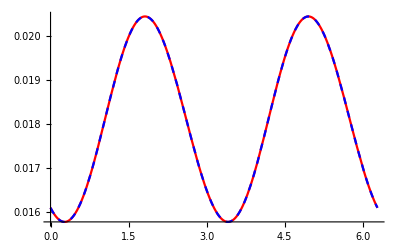

```mathematica
Plot[{J2[{Cos[ϕ],Sin[ϕ]},{0.0,0.0},{0.9237949693169148,0.9933558220768413},{0.8906088551297885,0.5034137135325174},{1.0671192399522245,0.2037332952522504},{0.1152369628812383,0.9584092012785702}],J2HZ[{Cos[ϕ],Sin[ϕ]},{0.0,0.0},{0.9237949693169148,0.9933558220768413},{0.8906088551297885,0.5034137135325174},{1.0671192399522245,0.2037332952522504},{0.1152369628812383,0.9584092012785702}]},{ϕ,0,2π},PlotStyle->{{Red},{Blue,Dashed}}]
```

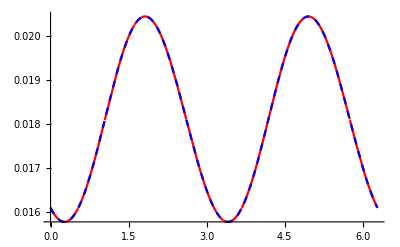
```mathematica
0000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000-Graphics-
```

## Dipole Cross Section

```mathematica
LaunchKernels[100];
$KernelCount
```

100

```mathematica
dσ[{x1_,y1_},{x2_,y2_},{x3_,y3_},{x4_,y4_},{kT_,ϕ_}]:=Module[{amp},
amp=J[{0,0},{x1,y1},{x2,y2},{x3,y3},{x4,y4},{kT Cos[ϕ],kT Sin[ϕ]}];
amp.Conjugate[amp]
]
```

```mathematica
dσHZ[{x1_,y1_},{x2_,y2_},{x3_,y3_},{x4_,y4_},{kT_,ϕ_}]:=Module[{amp},
J2HZ[{kT Cos[ϕ],kT Sin[ϕ]},{0,0},{x1,y1},{x2,y2},{x3,y3},{x4,y4}]
]
```

```mathematica
showdσ[bu_,x1u_,x3u_,kT_]:=Module[{ϕ,x2u,x4u,v2},
x2u=-x1u;x4u=-x3u;
Print[Show[Graphics[{Orange,Opacity[0.3],Disk[{0,0},0.6]}],Graphics[{Orange,Opacity[0.3],Disk[bu,0.6]}],Graphics[{Dashing[0.025],RGBColor[0,0.5,0],Thickness[0.01],Line[{x3u,x4u}]}],Graphics[{PointSize[0.05],Blue,Point[x3u]}],Graphics[{PointSize[0.05],Red,Point[x4u]}],Graphics[{Dashing[0.025],RGBColor[0,0.5,0],Thickness[0.01],Line[{bu+x1u,bu+x2u}]}],Graphics[{PointSize[0.05],Blue,Point[bu+x1u]}],Graphics[{PointSize[0.05],Red,Point[bu+x2u]}],Axes->True,LabelStyle->{Black,16},PlotLabel->"Dipole Orientation"]];
Print[""];
Print[Plot[dσ[x1u+bu/2,x2u+bu/2,x3u-bu/2,x4u-bu/2,{kT,ϕ}],{ϕ,0,2π}]];
Print[ParametricPlot[dσ[x1u+bu/2,x2u+bu/2,x3u-bu/2,x4u-bu/2,{kT,ϕ}]{Cos[ϕ],Sin[ϕ]},{ϕ,0,2π},PlotStyle->Red,AxesLabel->{x,y},LabelStyle->{Black,16},PlotLabel->"dσ/d^2{Cos[ϕ],Sin[ϕ]}"]];
v2=NIntegrate[dσ[x1u+bu/2,x2u+bu/2,x3u-bu/2,x4u-bu/2,{kT,ϕ}] {Cos[2(ϕ)],Sin[2(ϕ)]},{ϕ,0,2π}]/NIntegrate[dσ[x1u+bu/2,x2u+bu/2,x3u-bu/2,x4u-bu/2,{kT,ϕ}],{ϕ,0,2π}];
Print["v_2=",v2];
v2
]
```

```mathematica
showdσHZ[bu_,x1u_,x3u_,kT_,showQ_:True]:=Module[{ϕ,x2u,x4u,p1,p2,p3},
x2u=-x1u;x4u=-x3u;
If[showQ,
p1=Show[Graphics[{Orange,Opacity[0.3],Disk[{0,0},0.6]}],Graphics[{Orange,Opacity[0.3],Disk[bu,0.6]}],Graphics[{Dashing[0.025],RGBColor[0,0.5,0],Thickness[0.01],Line[{x3u,x4u}]}],Graphics[{PointSize[0.05],Blue,Point[x3u]}],Graphics[{PointSize[0.05],Red,Point[x4u]}],Graphics[{Dashing[0.025],RGBColor[0,0.5,0],Thickness[0.01],Line[{bu+x1u,bu+x2u}]}],Graphics[{PointSize[0.05],Blue,Point[bu+x1u]}],Graphics[{PointSize[0.05],Red,Point[bu+x2u]}],Axes->True,LabelStyle->{Black,16},PlotLabel->"Dipole Orientation"];
p2=Plot[dσHZ[x1u+bu/2,x2u+bu/2,x3u-bu/2,x4u-bu/2,{kT,ϕ}],{ϕ,0,2π}];
p3=ParametricPlot[dσHZ[x1u+bu/2,x2u+bu/2,x3u-bu/2,x4u-bu/2,{kT,ϕ}]{Cos[ϕ],Sin[ϕ]},{ϕ,0,2π},PlotStyle->Red,AxesLabel->{x,y},LabelStyle->{Black,16}(*,PlotLabel->"dσ/d^2{Cos[ϕ],Sin[ϕ]}"*)];
Print[GraphicsRow[{p1,p3,p2},ImageSize->1000]];
];
NIntegrate[dσHZ[x1u+bu/2,x2u+bu/2,x3u-bu/2,x4u-bu/2,{kT,ϕ}] {Cos[2(ϕ)],Sin[2(ϕ)]},{ϕ,0,2π}]/NIntegrate[dσHZ[x1u+bu/2,x2u+bu/2,x3u-bu/2,x4u-bu/2,{kT,ϕ}],{ϕ,0,2π}]
]
```

```mathematica
showdσHZ[n_,bu_,x1u_,x3u_,kT_,showQ_:True]:=Module[{ϕ,x2u,x4u,p1,p2,p3},
x2u=-x1u;x4u=-x3u;
If[showQ,
p1=Show[Graphics[{Orange,Opacity[0.3],Disk[{0,0},0.6]}],Graphics[{Orange,Opacity[0.3],Disk[bu,0.6]}],Graphics[{Dashing[0.025],RGBColor[0,0.5,0],Thickness[0.01],Line[{x3u,x4u}]}],Graphics[{PointSize[0.05],Blue,Point[x3u]}],Graphics[{PointSize[0.05],Red,Point[x4u]}],Graphics[{Dashing[0.025],RGBColor[0,0.5,0],Thickness[0.01],Line[{bu+x1u,bu+x2u}]}],Graphics[{PointSize[0.05],Blue,Point[bu+x1u]}],Graphics[{PointSize[0.05],Red,Point[bu+x2u]}],Axes->True,LabelStyle->{Black,16},PlotLabel->"Dipole Orientation"];
p2=Plot[dσHZ[x1u+bu/2,x2u+bu/2,x3u-bu/2,x4u-bu/2,{kT,ϕ}],{ϕ,0,2π}];
p3=ParametricPlot[dσHZ[x1u+bu/2,x2u+bu/2,x3u-bu/2,x4u-bu/2,{kT,ϕ}]{Cos[ϕ],Sin[ϕ]},{ϕ,0,2π},PlotStyle->Red,AxesLabel->{x,y},LabelStyle->{Black,16}(*,PlotLabel->"dσ/d^2{Cos[ϕ],Sin[ϕ]}"*)];
Print[GraphicsRow[{p1,p3,p2},ImageSize->1000]];
];
NIntegrate[dσHZ[x1u+bu/2,x2u+bu/2,x3u-bu/2,x4u-bu/2,{kT,ϕ}] {Cos[n(ϕ)],Sin[n(ϕ)]},{ϕ,0,2π}]/NIntegrate[dσHZ[x1u+bu/2,x2u+bu/2,x3u-bu/2,x4u-bu/2,{kT,ϕ}],{ϕ,0,2π}]
]
```

```mathematica
ParallelEvaluate[
ClearAll[showdσHZ];
showdσHZ[n_,bu_,x1u_,x3u_,kT_,showQ_:True]:=Module[{ϕ,x2u,x4u,p1,p2,p3,num,den},
x2u=-x1u;x4u=-x3u;
num=NIntegrate[dσHZ[x1u+bu/2,x2u+bu/2,x3u-bu/2,x4u-bu/2,{kT,ϕ}] {Cos[n(ϕ)],Sin[n(ϕ)]},{ϕ,0,2π}];
den=NIntegrate[dσHZ[x1u+bu/2,x2u+bu/2,x3u-bu/2,x4u-bu/2,{kT,ϕ}],{ϕ,0,2π}];
num/den
]
];
```

## b=2 r_dp

```mathematica
Getv2kT[b_,θA_:π/2,θB_:π/2]:=Module[{v2kTb05,i,kT,x1u,x3u,bu,ti},
ti=AbsoluteTime[];
x1u=1/2{Cos[θA],Sin[θA]};
x3u=1/2{Cos[θB],Sin[θB]};
bu={b,0};
v2kTb05=ParallelTable[{kT,showdσHZ[2,bu,x1u,x3u,kT,False]},{kT,0.1,10,0.1}];
Print[ListPlot[{Transpose[{v2kTb05[[All,1]],Re[v2kTb05[[All,2,1]]]}]},PlotStyle->{Red,Blue}]];
Print["Computatino time: ", AbsoluteTime[]-ti];
Print["b=",b, ", θA=",θA,", θB=",θB];
v2kTb05
]
```

## Dipole v_2

```mathematica
ParallelEvaluate[
ClearAll[v2HZ];
v2HZ[kT_,b_,rA_,rB_]:=Module[{num,den,n},
n=2;
Print[kT, " starts to run on kern ", $KernelID];
num=NIntegrate[dσHZ[{b/2+1/2 rA Cos[ϕA],1/2 rA Sin[ϕA]},{b/2-1/2 rA Cos[ϕA],-1/2 rA Sin[ϕA]},{-b/2+1/2 rB Cos[ϕB],1/2 rB Sin[ϕB]},{-b/2-1/2 rB Cos[ϕB],-1/2 rB Sin[ϕB]},{kT,ϕ}] Cos[n(ϕ)],{ϕ,0,2π},{ϕA,0,2π},{ϕB,0,2π},Method->{"MonteCarlo"}];
Print[kT, "finishes num on kern ", $KernelID];
den=NIntegrate[dσHZ[{b/2+1/2 rA Cos[ϕA],1/2 rA Sin[ϕA]},{b/2-1/2 rA Cos[ϕA],-1/2 rA Sin[ϕA]},{-b/2+1/2 rB Cos[ϕB],1/2 rB Sin[ϕB]},{-b/2-1/2 rB Cos[ϕB],-1/2 rB Sin[ϕB]},{kT,ϕ}],{ϕ,0,2π},{ϕA,0,2π},{ϕB,0,2π},Method->{"MonteCarlo"}];
Print["Main calculation is done on kern ", $KernelID, " with k_T=",kT];
{num,den,num/den}
]
];
```

```mathematica
ParallelEvaluate[
ClearAll[v2HZ];
v2HZ[kT_,b_,rA_,rB_, nMC_:10^4]:=Module[{num,den,n},
n=2;
Print[kT, " starts to run on kern ", $KernelID, " at ", Now];
num=NIntegrate[dσ[{b/2+1/2 rA Cos[ϕA],1/2 rA Sin[ϕA]},{b/2-1/2 rA Cos[ϕA],-1/2 rA Sin[ϕA]},{-b/2+1/2 rB Cos[ϕB],1/2 rB Sin[ϕB]},{-b/2-1/2 rB Cos[ϕB],-1/2 rB Sin[ϕB]},{kT,ϕ}] Cos[n(ϕ)],{ϕ,0,2π},{ϕA,0,2π},{ϕB,0,2π},Method->{"AdaptiveMonteCarlo",Method->{"MonteCarloRule","Points"->nMC}}];
Print[kT, " finishes num on kern ", $KernelID, " at ", Now];
den=NIntegrate[dσ[{b/2+1/2 rA Cos[ϕA],1/2 rA Sin[ϕA]},{b/2-1/2 rA Cos[ϕA],-1/2 rA Sin[ϕA]},{-b/2+1/2 rB Cos[ϕB],1/2 rB Sin[ϕB]},{-b/2-1/2 rB Cos[ϕB],-1/2 rB Sin[ϕB]},{kT,ϕ}],{ϕ,0,2π},{ϕA,0,2π},{ϕB,0,2π},Method->{"AdaptiveMonteCarlo",Method->{"MonteCarloRule","Points"->nMC}}];
Print["Main calculation is done on kern ", $KernelID, " with k_T=",kT, " at ", Now];
{num,den,num/den}
]
];
```

```mathematica
{$MaxLicenseProcesses, $MaxLicenseSubprocesses}
```

{∞,∞}

```mathematica
ParallelTable[{k,v2HZ[k,2.0,1.0,1.0]},{k,0.1,10,0.2}]
```

0.1 starts to run on kern 100 at Fri 3 Feb 2023 20:22:16GMT+1

0.3 starts to run on kern 99 at Fri 3 Feb 2023 20:22:16GMT+1

0.5 starts to run on kern 98 at Fri 3 Feb 2023 20:22:16GMT+1

0.7 starts to run on kern 97 at Fri 3 Feb 2023 20:22:16GMT+1

0.9 starts to run on kern 96 at Fri 3 Feb 2023 20:22:16GMT+1

1.1 starts to run on kern 95 at Fri 3 Feb 2023 20:22:16GMT+1

1.3 starts to run on kern 94 at Fri 3 Feb 2023 20:22:16GMT+1

1.5 starts to run on kern 93 at Fri 3 Feb 2023 20:22:16GMT+1

1.7 starts to run on kern 92 at Fri 3 Feb 2023 20:22:16GMT+1

1.9 starts to run on kern 91 at Fri 3 Feb 2023 20:22:16GMT+1

2.1 starts to run on kern 90 at Fri 3 Feb 2023 20:22:16GMT+1

2.3 starts to run on kern 89 at Fri 3 Feb 2023 20:22:16GMT+1

2.5 starts to run on kern 88 at Fri 3 Feb 2023 20:22:16GMT+1

2.7 starts to run on kern 87 at Fri 3 Feb 2023 20:22:16GMT+1

2.9 starts to run on kern 86 at Fri 3 Feb 2023 20:22:16GMT+1

3.1 starts to run on kern 85 at Fri 3 Feb 2023 20:22:16GMT+1

3.3 starts to run on kern 84 at Fri 3 Feb 2023 20:22:16GMT+1

3.5 starts to run on kern 83 at Fri 3 Feb 2023 20:22:16GMT+1

3.7 starts to run on kern 82 at Fri 3 Feb 2023 20:22:16GMT+1

3.9 starts to run on kern 81 at Fri 3 Feb 2023 20:22:16GMT+1

4.1 starts to run on kern 80 at Fri 3 Feb 2023 20:22:16GMT+1

4.3 starts to run on kern 79 at Fri 3 Feb 2023 20:22:16GMT+1

4.5 starts to run on kern 78 at Fri 3 Feb 2023 20:22:16GMT+1

4.7 starts to run on kern 77 at Fri 3 Feb 2023 20:22:16GMT+1

4.9 starts to run on kern 76 at Fri 3 Feb 2023 20:22:16GMT+1

5.1 starts to run on kern 75 at Fri 3 Feb 2023 20:22:16GMT+1

5.3 starts to run on kern 74 at Fri 3 Feb 2023 20:22:16GMT+1

5.5 starts to run on kern 73 at Fri 3 Feb 2023 20:22:16GMT+1

5.7 starts to run on kern 72 at Fri 3 Feb 2023 20:22:16GMT+1

5.9 starts to run on kern 71 at Fri 3 Feb 2023 20:22:16GMT+1

6.1 starts to run on kern 70 at Fri 3 Feb 2023 20:22:16GMT+1

6.3 starts to run on kern 69 at Fri 3 Feb 2023 20:22:16GMT+1

6.5 starts to run on kern 68 at Fri 3 Feb 2023 20:22:16GMT+1

6.7 starts to run on kern 67 at Fri 3 Feb 2023 20:22:16GMT+1

6.9 starts to run on kern 66 at Fri 3 Feb 2023 20:22:16GMT+1

7.1 starts to run on kern 65 at Fri 3 Feb 2023 20:22:16GMT+1

7.3 starts to run on kern 64 at Fri 3 Feb 2023 20:22:16GMT+1

7.5 starts to run on kern 63 at Fri 3 Feb 2023 20:22:16GMT+1

7.7 starts to run on kern 62 at Fri 3 Feb 2023 20:22:16GMT+1

7.9 starts to run on kern 61 at Fri 3 Feb 2023 20:22:16GMT+1

8.1 starts to run on kern 60 at Fri 3 Feb 2023 20:22:16GMT+1

8.3 starts to run on kern 59 at Fri 3 Feb 2023 20:22:16GMT+1

8.5 starts to run on kern 58 at Fri 3 Feb 2023 20:22:16GMT+1

8.7 starts to run on kern 57 at Fri 3 Feb 2023 20:22:16GMT+1

8.9 starts to run on kern 56 at Fri 3 Feb 2023 20:22:16GMT+1

9.1 starts to run on kern 55 at Fri 3 Feb 2023 20:22:16GMT+1

9.3 starts to run on kern 54 at Fri 3 Feb 2023 20:22:16GMT+1

9.5 starts to run on kern 53 at Fri 3 Feb 2023 20:22:16GMT+1

9.7 starts to run on kern 52 at Fri 3 Feb 2023 20:22:16GMT+1

9.9 starts to run on kern 51 at Fri 3 Feb 2023 20:22:16GMT+1

3.9 finishes num on kern 81 at Fri 3 Feb 2023 20:30:08GMT+1

Main calculation is done on kern 81 with k_T=3.9 at Fri 3 Feb 2023 20:30:53GMT+1

3.3 finishes num on kern 84 at Fri 3 Feb 2023 20:31:52GMT+1

4.7 finishes num on kern 77 at Fri 3 Feb 2023 20:31:55GMT+1

4.5 finishes num on kern 78 at Fri 3 Feb 2023 20:31:55GMT+1

Main calculation is done on kern 84 with k_T=3.3 at Fri 3 Feb 2023 20:32:30GMT+1

4.9 finishes num on kern 76 at Fri 3 Feb 2023 20:32:30GMT+1

Main calculation is done on kern 77 with k_T=4.7 at Fri 3 Feb 2023 20:32:39GMT+1

Main calculation is done on kern 78 with k_T=4.5 at Fri 3 Feb 2023 20:32:39GMT+1

5.1 finishes num on kern 75 at Fri 3 Feb 2023 20:33:10GMT+1

Main calculation is done on kern 76 with k_T=4.9 at Fri 3 Feb 2023 20:33:16GMT+1

2.5 finishes num on kern 88 at Fri 3 Feb 2023 20:33:21GMT+1

5.3 finishes num on kern 74 at Fri 3 Feb 2023 20:33:42GMT+1

3.1 finishes num on kern 85 at Fri 3 Feb 2023 20:33:43GMT+1

6.1 finishes num on kern 70 at Fri 3 Feb 2023 20:33:54GMT+1

Main calculation is done on kern 88 with k_T=2.5 at Fri 3 Feb 2023 20:33:58GMT+1

Main calculation is done on kern 75 with k_T=5.1 at Fri 3 Feb 2023 20:34:01GMT+1

4.3 finishes num on kern 79 at Fri 3 Feb 2023 20:34:18GMT+1

Main calculation is done on kern 85 with k_T=3.1 at Fri 3 Feb 2023 20:34:21GMT+1

Main calculation is done on kern 74 with k_T=5.3 at Fri 3 Feb 2023 20:34:34GMT+1

Main calculation is done on kern 79 with k_T=4.3 at Fri 3 Feb 2023 20:34:56GMT+1

5.5 finishes num on kern 73 at Fri 3 Feb 2023 20:35:42GMT+1

2.9 finishes num on kern 86 at Fri 3 Feb 2023 20:36:12GMT+1

5.7 finishes num on kern 72 at Fri 3 Feb 2023 20:36:22GMT+1

Main calculation is done on kern 70 with k_T=6.1 at Fri 3 Feb 2023 20:36:40GMT+1

4.1 finishes num on kern 80 at Fri 3 Feb 2023 20:36:42GMT+1

Main calculation is done on kern 86 with k_T=2.9 at Fri 3 Feb 2023 20:36:47GMT+1

2.7 finishes num on kern 87 at Fri 3 Feb 2023 20:37:05GMT+1

Main calculation is done on kern 80 with k_T=4.1 at Fri 3 Feb 2023 20:37:20GMT+1

Main calculation is done on kern 87 with k_T=2.7 at Fri 3 Feb 2023 20:37:40GMT+1

5.9 finishes num on kern 71 at Fri 3 Feb 2023 20:37:42GMT+1

Main calculation is done on kern 73 with k_T=5.5 at Fri 3 Feb 2023 20:38:07GMT+1

Main calculation is done on kern 72 with k_T=5.7 at Fri 3 Feb 2023 20:38:52GMT+1

3.7 finishes num on kern 82 at Fri 3 Feb 2023 20:38:59GMT+1

Main calculation is done on kern 82 with k_T=3.7 at Fri 3 Feb 2023 20:39:31GMT+1

Main calculation is done on kern 71 with k_T=5.9 at Fri 3 Feb 2023 20:40:12GMT+1

3.5 finishes num on kern 83 at Fri 3 Feb 2023 20:41:00GMT+1

Main calculation is done on kern 83 with k_T=3.5 at Fri 3 Feb 2023 20:41:32GMT+1

6.9 finishes num on kern 66 at Fri 3 Feb 2023 20:42:03GMT+1

Main calculation is done on kern 66 with k_T=6.9 at Fri 3 Feb 2023 20:43:02GMT+1

6.3 finishes num on kern 69 at Fri 3 Feb 2023 20:43:30GMT+1

6.5 finishes num on kern 68 at Fri 3 Feb 2023 20:44:30GMT+1

Main calculation is done on kern 69 with k_T=6.3 at Fri 3 Feb 2023 20:46:03GMT+1

Main calculation is done on kern 68 with k_T=6.5 at Fri 3 Feb 2023 20:47:03GMT+1

2.1 finishes num on kern 90 at Fri 3 Feb 2023 20:48:28GMT+1

Main calculation is done on kern 90 with k_T=2.1 at Fri 3 Feb 2023 20:48:57GMT+1

7.5 finishes num on kern 63 at Fri 3 Feb 2023 20:49:32GMT+1

Main calculation is done on kern 63 with k_T=7.5 at Fri 3 Feb 2023 20:50:32GMT+1

6.7 finishes num on kern 67 at Fri 3 Feb 2023 20:53:30GMT+1

Main calculation is done on kern 67 with k_T=6.7 at Fri 3 Feb 2023 20:54:23GMT+1

7.9 finishes num on kern 61 at Fri 3 Feb 2023 20:57:16GMT+1

Main calculation is done on kern 61 with k_T=7.9 at Fri 3 Feb 2023 20:58:18GMT+1

2.3 finishes num on kern 89 at Fri 3 Feb 2023 20:59:06GMT+1

7.1 finishes num on kern 65 at Fri 3 Feb 2023 20:59:14GMT+1

Main calculation is done on kern 89 with k_T=2.3 at Fri 3 Feb 2023 20:59:35GMT+1

Main calculation is done on kern 65 with k_T=7.1 at Fri 3 Feb 2023 21:00:10GMT+1

NIntegrate::maxp: The integral failed to converge after 1010000 integrand evaluations. NIntegrate obtained -0.0594753+0. ⅈ and 0.00270183 for the integral and error estimates.

0.3 finishes num on kern 99 at Fri 3 Feb 2023 21:06:19GMT+1

Main calculation is done on kern 99 with k_T=0.3 at Fri 3 Feb 2023 21:06:43GMT+1

NIntegrate::maxp: The integral failed to converge after 1010000 integrand evaluations. NIntegrate obtained -0.0748892+0. ⅈ and 0.023912 for the integral and error estimates.

0.1 finishes num on kern 100 at Fri 3 Feb 2023 21:07:01GMT+1

8.1 finishes num on kern 60 at Fri 3 Feb 2023 21:07:15GMT+1

Main calculation is done on kern 100 with k_T=0.1 at Fri 3 Feb 2023 21:07:25GMT+1

7.3 finishes num on kern 64 at Fri 3 Feb 2023 21:07:29GMT+1

NIntegrate::maxp: The integral failed to converge after 1010000 integrand evaluations. NIntegrate obtained -0.0218069+0. ⅈ and 0.000611931 for the integral and error estimates.

0.5 finishes num on kern 98 at Fri 3 Feb 2023 21:07:56GMT+1

Main calculation is done on kern 60 with k_T=8.1 at Fri 3 Feb 2023 21:08:16GMT+1

Main calculation is done on kern 98 with k_T=0.5 at Fri 3 Feb 2023 21:08:20GMT+1

Main calculation is done on kern 64 with k_T=7.3 at Fri 3 Feb 2023 21:08:25GMT+1

NIntegrate::maxp: The integral failed to converge after 1010000 integrand evaluations. NIntegrate obtained 0.0122469+0. ⅈ and 0.000211282 for the integral and error estimates.

1.1 finishes num on kern 95 at Fri 3 Feb 2023 21:10:03GMT+1

NIntegrate::maxp: The integral failed to converge after 1010000 integrand evaluations. NIntegrate obtained -0.00024595+0. ⅈ and 0.000407189 for the integral and error estimates.

0.7 finishes num on kern 97 at Fri 3 Feb 2023 21:10:13GMT+1

NIntegrate::maxp: The integral failed to converge after 1010000 integrand evaluations. NIntegrate obtained 0.00999454+0. ⅈ and 0.000172592 for the integral and error estimates.

0.9 finishes num on kern 96 at Fri 3 Feb 2023 21:10:21GMT+1

Main calculation is done on kern 95 with k_T=1.1 at Fri 3 Feb 2023 21:10:29GMT+1

Main calculation is done on kern 97 with k_T=0.7 at Fri 3 Feb 2023 21:10:39GMT+1

Main calculation is done on kern 96 with k_T=0.9 at Fri 3 Feb 2023 21:10:47GMT+1

NIntegrate::maxp: The integral failed to converge after 1010000 integrand evaluations. NIntegrate obtained 0.00593628+0. ⅈ and 0.0000934312 for the integral and error estimates.

1.5 finishes num on kern 93 at Fri 3 Feb 2023 21:10:54GMT+1

NIntegrate::maxp: The integral failed to converge after 1010000 integrand evaluations. NIntegrate obtained 0.00996087+0. ⅈ and 0.000150595 for the integral and error estimates.

1.3 finishes num on kern 94 at Fri 3 Feb 2023 21:11:11GMT+1

Main calculation is done on kern 93 with k_T=1.5 at Fri 3 Feb 2023 21:11:21GMT+1

Main calculation is done on kern 94 with k_T=1.3 at Fri 3 Feb 2023 21:11:37GMT+1

NIntegrate::maxp: The integral failed to converge after 1010000 integrand evaluations. NIntegrate obtained 0.00155203+0. ⅈ and 0.0000388981 for the integral and error estimates.

1.7 finishes num on kern 92 at Fri 3 Feb 2023 21:12:08GMT+1

Main calculation is done on kern 92 with k_T=1.7 at Fri 3 Feb 2023 21:12:34GMT+1

NIntegrate::maxp: The integral failed to converge after 1010000 integrand evaluations. NIntegrate obtained -0.00196139+0. ⅈ and 0.0000409027 for the integral and error estimates.

1.9 finishes num on kern 91 at Fri 3 Feb 2023 21:12:56GMT+1

Main calculation is done on kern 91 with k_T=1.9 at Fri 3 Feb 2023 21:13:23GMT+1

7.7 finishes num on kern 62 at Fri 3 Feb 2023 21:33:03GMT+1

Main calculation is done on kern 62 with k_T=7.7 at Fri 3 Feb 2023 21:34:02GMT+1

```mathematica
Export["b20.dat",%]
```

```mathematica
(*AdapativeMonteCarlo*)
ParallelTable[{k,v2HZ[k,2.0,1.0,1.0]},{k,0.1,10,0.1}]
```

0.2 starts to run on kern 99 at Fri 3 Feb 2023 16:25:26GMT+1

0.3 starts to run on kern 98 at Fri 3 Feb 2023 16:25:26GMT+1

1.2 starts to run on kern 89 at Fri 3 Feb 2023 16:25:26GMT+1

2.1 starts to run on kern 80 at Fri 3 Feb 2023 16:25:26GMT+1

2.3 starts to run on kern 78 at Fri 3 Feb 2023 16:25:26GMT+1

2.5 starts to run on kern 76 at Fri 3 Feb 2023 16:25:26GMT+1

2.6 starts to run on kern 75 at Fri 3 Feb 2023 16:25:26GMT+1

2.7 starts to run on kern 74 at Fri 3 Feb 2023 16:25:26GMT+1

2.8 starts to run on kern 73 at Fri 3 Feb 2023 16:25:26GMT+1

2.9 starts to run on kern 72 at Fri 3 Feb 2023 16:25:26GMT+1

3. starts to run on kern 71 at Fri 3 Feb 2023 16:25:26GMT+1

3.1 starts to run on kern 70 at Fri 3 Feb 2023 16:25:26GMT+1

3.2 starts to run on kern 69 at Fri 3 Feb 2023 16:25:26GMT+1

3.3 starts to run on kern 68 at Fri 3 Feb 2023 16:25:26GMT+1

3.4 starts to run on kern 67 at Fri 3 Feb 2023 16:25:26GMT+1

3.5 starts to run on kern 66 at Fri 3 Feb 2023 16:25:26GMT+1

3.6 starts to run on kern 65 at Fri 3 Feb 2023 16:25:26GMT+1

3.7 starts to run on kern 64 at Fri 3 Feb 2023 16:25:26GMT+1

3.8 starts to run on kern 63 at Fri 3 Feb 2023 16:25:26GMT+1

3.9 starts to run on kern 62 at Fri 3 Feb 2023 16:25:26GMT+1

4. starts to run on kern 61 at Fri 3 Feb 2023 16:25:26GMT+1

4.1 starts to run on kern 60 at Fri 3 Feb 2023 16:25:26GMT+1

4.2 starts to run on kern 59 at Fri 3 Feb 2023 16:25:26GMT+1

4.3 starts to run on kern 58 at Fri 3 Feb 2023 16:25:26GMT+1

4.4 starts to run on kern 57 at Fri 3 Feb 2023 16:25:26GMT+1

4.5 starts to run on kern 56 at Fri 3 Feb 2023 16:25:26GMT+1

4.6 starts to run on kern 55 at Fri 3 Feb 2023 16:25:26GMT+1

4.7 starts to run on kern 54 at Fri 3 Feb 2023 16:25:26GMT+1

4.8 starts to run on kern 53 at Fri 3 Feb 2023 16:25:26GMT+1

4.9 starts to run on kern 52 at Fri 3 Feb 2023 16:25:26GMT+1

5. starts to run on kern 51 at Fri 3 Feb 2023 16:25:26GMT+1

5.1 starts to run on kern 50 at Fri 3 Feb 2023 16:25:26GMT+1

5.2 starts to run on kern 49 at Fri 3 Feb 2023 16:25:26GMT+1

5.3 starts to run on kern 48 at Fri 3 Feb 2023 16:25:26GMT+1

5.4 starts to run on kern 47 at Fri 3 Feb 2023 16:25:26GMT+1

5.5 starts to run on kern 46 at Fri 3 Feb 2023 16:25:26GMT+1

5.6 starts to run on kern 45 at Fri 3 Feb 2023 16:25:26GMT+1

5.7 starts to run on kern 44 at Fri 3 Feb 2023 16:25:26GMT+1

5.8 starts to run on kern 43 at Fri 3 Feb 2023 16:25:26GMT+1

5.9 starts to run on kern 42 at Fri 3 Feb 2023 16:25:26GMT+1

6. starts to run on kern 41 at Fri 3 Feb 2023 16:25:26GMT+1

6.1 starts to run on kern 40 at Fri 3 Feb 2023 16:25:26GMT+1

6.2 starts to run on kern 39 at Fri 3 Feb 2023 16:25:26GMT+1

6.3 starts to run on kern 38 at Fri 3 Feb 2023 16:25:26GMT+1

6.4 starts to run on kern 37 at Fri 3 Feb 2023 16:25:26GMT+1

6.5 starts to run on kern 36 at Fri 3 Feb 2023 16:25:26GMT+1

6.6 starts to run on kern 35 at Fri 3 Feb 2023 16:25:26GMT+1

6.7 starts to run on kern 34 at Fri 3 Feb 2023 16:25:26GMT+1

6.8 starts to run on kern 33 at Fri 3 Feb 2023 16:25:26GMT+1

6.9 starts to run on kern 32 at Fri 3 Feb 2023 16:25:26GMT+1

7. starts to run on kern 31 at Fri 3 Feb 2023 16:25:26GMT+1

7.1 starts to run on kern 30 at Fri 3 Feb 2023 16:25:26GMT+1

7.2 starts to run on kern 29 at Fri 3 Feb 2023 16:25:26GMT+1

7.3 starts to run on kern 28 at Fri 3 Feb 2023 16:25:26GMT+1

7.4 starts to run on kern 27 at Fri 3 Feb 2023 16:25:26GMT+1

7.5 starts to run on kern 26 at Fri 3 Feb 2023 16:25:26GMT+1

7.6 starts to run on kern 25 at Fri 3 Feb 2023 16:25:26GMT+1

7.7 starts to run on kern 24 at Fri 3 Feb 2023 16:25:26GMT+1

7.8 starts to run on kern 23 at Fri 3 Feb 2023 16:25:26GMT+1

7.9 starts to run on kern 22 at Fri 3 Feb 2023 16:25:26GMT+1

8. starts to run on kern 21 at Fri 3 Feb 2023 16:25:26GMT+1

8.1 starts to run on kern 20 at Fri 3 Feb 2023 16:25:26GMT+1

8.2 starts to run on kern 19 at Fri 3 Feb 2023 16:25:26GMT+1

8.3 starts to run on kern 18 at Fri 3 Feb 2023 16:25:26GMT+1

8.4 starts to run on kern 17 at Fri 3 Feb 2023 16:25:26GMT+1

8.5 starts to run on kern 16 at Fri 3 Feb 2023 16:25:26GMT+1

8.6 starts to run on kern 15 at Fri 3 Feb 2023 16:25:26GMT+1

8.7 starts to run on kern 14 at Fri 3 Feb 2023 16:25:26GMT+1

8.8 starts to run on kern 13 at Fri 3 Feb 2023 16:25:26GMT+1

8.9 starts to run on kern 12 at Fri 3 Feb 2023 16:25:26GMT+1

9. starts to run on kern 11 at Fri 3 Feb 2023 16:25:26GMT+1

9.1 starts to run on kern 10 at Fri 3 Feb 2023 16:25:26GMT+1

9.2 starts to run on kern 9 at Fri 3 Feb 2023 16:25:26GMT+1

9.3 starts to run on kern 8 at Fri 3 Feb 2023 16:25:26GMT+1

9.4 starts to run on kern 7 at Fri 3 Feb 2023 16:25:26GMT+1

9.5 starts to run on kern 6 at Fri 3 Feb 2023 16:25:26GMT+1

9.6 starts to run on kern 5 at Fri 3 Feb 2023 16:25:26GMT+1

9.7 starts to run on kern 4 at Fri 3 Feb 2023 16:25:26GMT+1

9.8 starts to run on kern 3 at Fri 3 Feb 2023 16:25:26GMT+1

9.9 starts to run on kern 2 at Fri 3 Feb 2023 16:25:26GMT+1

10. starts to run on kern 1 at Fri 3 Feb 2023 16:25:26GMT+1

0.1 starts to run on kern 100 at Fri 3 Feb 2023 16:25:26GMT+1

0.4 starts to run on kern 97 at Fri 3 Feb 2023 16:25:26GMT+1

0.5 starts to run on kern 96 at Fri 3 Feb 2023 16:25:26GMT+1

0.6 starts to run on kern 95 at Fri 3 Feb 2023 16:25:26GMT+1

0.7 starts to run on kern 94 at Fri 3 Feb 2023 16:25:26GMT+1

0.8 starts to run on kern 93 at Fri 3 Feb 2023 16:25:26GMT+1

0.9 starts to run on kern 92 at Fri 3 Feb 2023 16:25:26GMT+1

1. starts to run on kern 91 at Fri 3 Feb 2023 16:25:26GMT+1

1.1 starts to run on kern 90 at Fri 3 Feb 2023 16:25:26GMT+1

1.3 starts to run on kern 88 at Fri 3 Feb 2023 16:25:26GMT+1

1.4 starts to run on kern 87 at Fri 3 Feb 2023 16:25:26GMT+1

1.5 starts to run on kern 86 at Fri 3 Feb 2023 16:25:26GMT+1

1.6 starts to run on kern 85 at Fri 3 Feb 2023 16:25:26GMT+1

1.7 starts to run on kern 84 at Fri 3 Feb 2023 16:25:26GMT+1

1.8 starts to run on kern 83 at Fri 3 Feb 2023 16:25:26GMT+1

1.9 starts to run on kern 82 at Fri 3 Feb 2023 16:25:26GMT+1

2. starts to run on kern 81 at Fri 3 Feb 2023 16:25:26GMT+1

2.2 starts to run on kern 79 at Fri 3 Feb 2023 16:25:26GMT+1

2.4 starts to run on kern 77 at Fri 3 Feb 2023 16:25:26GMT+1

4.8 finishes num on kern 53 at Fri 3 Feb 2023 16:36:24GMT+1

Main calculation is done on kern 53 with k_T=4.8 at Fri 3 Feb 2023 16:37:46GMT+1

3.8 finishes num on kern 63 at Fri 3 Feb 2023 16:37:57GMT+1

5.3 finishes num on kern 48 at Fri 3 Feb 2023 16:38:37GMT+1

Main calculation is done on kern 63 with k_T=3.8 at Fri 3 Feb 2023 16:39:08GMT+1

3.1 finishes num on kern 70 at Fri 3 Feb 2023 16:39:32GMT+1

4.9 finishes num on kern 52 at Fri 3 Feb 2023 16:39:53GMT+1

Main calculation is done on kern 48 with k_T=5.3 at Fri 3 Feb 2023 16:40:00GMT+1

Main calculation is done on kern 70 with k_T=3.1 at Fri 3 Feb 2023 16:40:33GMT+1

4. finishes num on kern 61 at Fri 3 Feb 2023 16:40:38GMT+1

5.2 finishes num on kern 49 at Fri 3 Feb 2023 16:40:53GMT+1

4.6 finishes num on kern 55 at Fri 3 Feb 2023 16:40:59GMT+1

Main calculation is done on kern 52 with k_T=4.9 at Fri 3 Feb 2023 16:41:15GMT+1

2.8 finishes num on kern 73 at Fri 3 Feb 2023 16:41:38GMT+1

3.2 finishes num on kern 69 at Fri 3 Feb 2023 16:41:42GMT+1

Main calculation is done on kern 61 with k_T=4. at Fri 3 Feb 2023 16:41:45GMT+1

4.7 finishes num on kern 54 at Fri 3 Feb 2023 16:41:47GMT+1

Main calculation is done on kern 55 with k_T=4.6 at Fri 3 Feb 2023 16:42:03GMT+1

Main calculation is done on kern 49 with k_T=5.2 at Fri 3 Feb 2023 16:42:14GMT+1

5. finishes num on kern 51 at Fri 3 Feb 2023 16:42:22GMT+1

Main calculation is done on kern 73 with k_T=2.8 at Fri 3 Feb 2023 16:42:42GMT+1

Main calculation is done on kern 69 with k_T=3.2 at Fri 3 Feb 2023 16:42:47GMT+1

4.3 finishes num on kern 58 at Fri 3 Feb 2023 16:42:54GMT+1

4.5 finishes num on kern 56 at Fri 3 Feb 2023 16:42:54GMT+1

Main calculation is done on kern 54 with k_T=4.7 at Fri 3 Feb 2023 16:42:59GMT+1

4.4 finishes num on kern 57 at Fri 3 Feb 2023 16:43:00GMT+1

5.8 finishes num on kern 43 at Fri 3 Feb 2023 16:43:00GMT+1

5.1 finishes num on kern 50 at Fri 3 Feb 2023 16:43:22GMT+1

6.1 finishes num on kern 40 at Fri 3 Feb 2023 16:43:42GMT+1

Main calculation is done on kern 51 with k_T=5. at Fri 3 Feb 2023 16:43:43GMT+1

Main calculation is done on kern 57 with k_T=4.4 at Fri 3 Feb 2023 16:43:55GMT+1

Main calculation is done on kern 56 with k_T=4.5 at Fri 3 Feb 2023 16:44:01GMT+1

3. finishes num on kern 71 at Fri 3 Feb 2023 16:44:03GMT+1

Main calculation is done on kern 58 with k_T=4.3 at Fri 3 Feb 2023 16:44:03GMT+1

5.4 finishes num on kern 47 at Fri 3 Feb 2023 16:44:15GMT+1

Main calculation is done on kern 50 with k_T=5.1 at Fri 3 Feb 2023 16:44:35GMT+1

Main calculation is done on kern 71 with k_T=3. at Fri 3 Feb 2023 16:45:11GMT+1

5.7 finishes num on kern 44 at Fri 3 Feb 2023 16:45:17GMT+1

Main calculation is done on kern 47 with k_T=5.4 at Fri 3 Feb 2023 16:45:36GMT+1

6. finishes num on kern 41 at Fri 3 Feb 2023 16:45:46GMT+1

4.2 finishes num on kern 59 at Fri 3 Feb 2023 16:46:49GMT+1

5.5 finishes num on kern 46 at Fri 3 Feb 2023 16:46:51GMT+1

Main calculation is done on kern 43 with k_T=5.8 at Fri 3 Feb 2023 16:47:01GMT+1

4.1 finishes num on kern 60 at Fri 3 Feb 2023 16:47:13GMT+1

6.4 finishes num on kern 37 at Fri 3 Feb 2023 16:47:19GMT+1

5.6 finishes num on kern 45 at Fri 3 Feb 2023 16:47:43GMT+1

Main calculation is done on kern 59 with k_T=4.2 at Fri 3 Feb 2023 16:47:53GMT+1

Main calculation is done on kern 40 with k_T=6.1 at Fri 3 Feb 2023 16:48:03GMT+1

Main calculation is done on kern 60 with k_T=4.1 at Fri 3 Feb 2023 16:48:17GMT+1

Main calculation is done on kern 44 with k_T=5.7 at Fri 3 Feb 2023 16:49:09GMT+1

Main calculation is done on kern 41 with k_T=6. at Fri 3 Feb 2023 16:50:01GMT+1

Main calculation is done on kern 46 with k_T=5.5 at Fri 3 Feb 2023 16:50:16GMT+1

3.9 finishes num on kern 62 at Fri 3 Feb 2023 16:50:23GMT+1

6.3 finishes num on kern 38 at Fri 3 Feb 2023 16:50:32GMT+1

2.6 finishes num on kern 75 at Fri 3 Feb 2023 16:50:47GMT+1

5.9 finishes num on kern 42 at Fri 3 Feb 2023 16:50:49GMT+1

Main calculation is done on kern 45 with k_T=5.6 at Fri 3 Feb 2023 16:51:09GMT+1

Main calculation is done on kern 62 with k_T=3.9 at Fri 3 Feb 2023 16:51:14GMT+1

3.7 finishes num on kern 64 at Fri 3 Feb 2023 16:51:37GMT+1

Main calculation is done on kern 75 with k_T=2.6 at Fri 3 Feb 2023 16:51:38GMT+1

Main calculation is done on kern 37 with k_T=6.4 at Fri 3 Feb 2023 16:51:41GMT+1

Main calculation is done on kern 64 with k_T=3.7 at Fri 3 Feb 2023 16:52:33GMT+1

3.6 finishes num on kern 65 at Fri 3 Feb 2023 16:53:31GMT+1

2.4 finishes num on kern 77 at Fri 3 Feb 2023 16:53:48GMT+1

Main calculation is done on kern 65 with k_T=3.6 at Fri 3 Feb 2023 16:54:19GMT+1

Main calculation is done on kern 38 with k_T=6.3 at Fri 3 Feb 2023 16:54:29GMT+1

Main calculation is done on kern 77 with k_T=2.4 at Fri 3 Feb 2023 16:54:33GMT+1

Main calculation is done on kern 42 with k_T=5.9 at Fri 3 Feb 2023 16:54:33GMT+1

3.5 finishes num on kern 66 at Fri 3 Feb 2023 16:55:12GMT+1

7.1 finishes num on kern 30 at Fri 3 Feb 2023 16:55:19GMT+1

Main calculation is done on kern 66 with k_T=3.5 at Fri 3 Feb 2023 16:55:57GMT+1

3.3 finishes num on kern 68 at Fri 3 Feb 2023 16:56:07GMT+1

Main calculation is done on kern 30 with k_T=7.1 at Fri 3 Feb 2023 16:56:39GMT+1

6.2 finishes num on kern 39 at Fri 3 Feb 2023 16:56:52GMT+1

Main calculation is done on kern 68 with k_T=3.3 at Fri 3 Feb 2023 16:57:03GMT+1

3.4 finishes num on kern 67 at Fri 3 Feb 2023 16:57:48GMT+1

7. finishes num on kern 31 at Fri 3 Feb 2023 16:58:04GMT+1

Main calculation is done on kern 67 with k_T=3.4 at Fri 3 Feb 2023 16:58:27GMT+1

2.9 finishes num on kern 72 at Fri 3 Feb 2023 16:58:51GMT+1

Main calculation is done on kern 31 with k_T=7. at Fri 3 Feb 2023 16:59:24GMT+1

Main calculation is done on kern 72 with k_T=2.9 at Fri 3 Feb 2023 16:59:30GMT+1

7.3 finishes num on kern 28 at Fri 3 Feb 2023 16:59:44GMT+1

Main calculation is done on kern 39 with k_T=6.2 at Fri 3 Feb 2023 17:00:11GMT+1

2.7 finishes num on kern 74 at Fri 3 Feb 2023 17:00:58GMT+1

Main calculation is done on kern 28 with k_T=7.3 at Fri 3 Feb 2023 17:01:06GMT+1

6.6 finishes num on kern 35 at Fri 3 Feb 2023 17:01:34GMT+1

Main calculation is done on kern 74 with k_T=2.7 at Fri 3 Feb 2023 17:01:41GMT+1

6.5 finishes num on kern 36 at Fri 3 Feb 2023 17:02:29GMT+1

Main calculation is done on kern 35 with k_T=6.6 at Fri 3 Feb 2023 17:02:46GMT+1

2.5 finishes num on kern 76 at Fri 3 Feb 2023 17:04:13GMT+1

Main calculation is done on kern 76 with k_T=2.5 at Fri 3 Feb 2023 17:04:51GMT+1

7.5 finishes num on kern 26 at Fri 3 Feb 2023 17:05:12GMT+1

2.1 finishes num on kern 80 at Fri 3 Feb 2023 17:05:16GMT+1

Main calculation is done on kern 36 with k_T=6.5 at Fri 3 Feb 2023 17:05:43GMT+1

Main calculation is done on kern 80 with k_T=2.1 at Fri 3 Feb 2023 17:05:52GMT+1

Main calculation is done on kern 26 with k_T=7.5 at Fri 3 Feb 2023 17:06:34GMT+1

7.6 finishes num on kern 25 at Fri 3 Feb 2023 17:08:25GMT+1

6.7 finishes num on kern 34 at Fri 3 Feb 2023 17:09:41GMT+1

Main calculation is done on kern 25 with k_T=7.6 at Fri 3 Feb 2023 17:09:46GMT+1

1.4 finishes num on kern 87 at Fri 3 Feb 2023 17:10:20GMT+1

Main calculation is done on kern 34 with k_T=6.7 at Fri 3 Feb 2023 17:10:47GMT+1

Main calculation is done on kern 87 with k_T=1.4 at Fri 3 Feb 2023 17:10:56GMT+1

2.3 finishes num on kern 78 at Fri 3 Feb 2023 17:13:00GMT+1

6.8 finishes num on kern 33 at Fri 3 Feb 2023 17:13:15GMT+1

Main calculation is done on kern 78 with k_T=2.3 at Fri 3 Feb 2023 17:13:38GMT+1

6.9 finishes num on kern 32 at Fri 3 Feb 2023 17:14:12GMT+1

Main calculation is done on kern 33 with k_T=6.8 at Fri 3 Feb 2023 17:14:20GMT+1

Main calculation is done on kern 32 with k_T=6.9 at Fri 3 Feb 2023 17:15:18GMT+1

1.5 finishes num on kern 86 at Fri 3 Feb 2023 17:18:46GMT+1

Main calculation is done on kern 86 with k_T=1.5 at Fri 3 Feb 2023 17:19:20GMT+1

7.2 finishes num on kern 29 at Fri 3 Feb 2023 17:22:59GMT+1

Main calculation is done on kern 29 with k_T=7.2 at Fri 3 Feb 2023 17:24:06GMT+1

NIntegrate::maxp: The integral failed to converge after 1010000 integrand evaluations. NIntegrate obtained -0.0697736+0. ⅈ and 0.00374444 for the integral and error estimates.

0.2 finishes num on kern 99 at Fri 3 Feb 2023 17:25:42GMT+1

NIntegrate::maxp: The integral failed to converge after 1010000 integrand evaluations. NIntegrate obtained -0.0535654+0. ⅈ and 0.00164494 for the integral and error estimates.

0.3 finishes num on kern 98 at Fri 3 Feb 2023 17:25:44GMT+1

NIntegrate::maxp: The integral failed to converge after 1010000 integrand evaluations. NIntegrate obtained -0.0212967+0. ⅈ and 0.000622331 for the integral and error estimates.

0.5 finishes num on kern 96 at Fri 3 Feb 2023 17:26:01GMT+1

Main calculation is done on kern 99 with k_T=0.2 at Fri 3 Feb 2023 17:26:10GMT+1

Main calculation is done on kern 98 with k_T=0.3 at Fri 3 Feb 2023 17:26:13GMT+1

NIntegrate::maxp: The integral failed to converge after 1010000 integrand evaluations. NIntegrate obtained -0.0370279+0. ⅈ and 0.000942661 for the integral and error estimates.

0.4 finishes num on kern 97 at Fri 3 Feb 2023 17:26:15GMT+1

NIntegrate::maxp: The integral failed to converge after 1010000 integrand evaluations. NIntegrate obtained -0.0648776+0. ⅈ and 0.0227567 for the integral and error estimates.

0.1 finishes num on kern 100 at Fri 3 Feb 2023 17:26:17GMT+1

Main calculation is done on kern 96 with k_T=0.5 at Fri 3 Feb 2023 17:26:29GMT+1

Main calculation is done on kern 97 with k_T=0.4 at Fri 3 Feb 2023 17:26:42GMT+1

Main calculation is done on kern 100 with k_T=0.1 at Fri 3 Feb 2023 17:26:45GMT+1

NIntegrate::maxp: The integral failed to converge after 1010000 integrand evaluations. NIntegrate obtained -0.00997658+0. ⅈ and 0.000424427 for the integral and error estimates.

0.6 finishes num on kern 95 at Fri 3 Feb 2023 17:28:32GMT+1

Main calculation is done on kern 95 with k_T=0.6 at Fri 3 Feb 2023 17:29:02GMT+1

2.2 finishes num on kern 79 at Fri 3 Feb 2023 17:29:36GMT+1

NIntegrate::maxp: The integral failed to converge after 1010000 integrand evaluations. NIntegrate obtained -0.000598204+0. ⅈ and 0.000567032 for the integral and error estimates.

0.7 finishes num on kern 94 at Fri 3 Feb 2023 17:29:38GMT+1

Main calculation is done on kern 94 with k_T=0.7 at Fri 3 Feb 2023 17:30:07GMT+1

Main calculation is done on kern 79 with k_T=2.2 at Fri 3 Feb 2023 17:30:08GMT+1

NIntegrate::maxp: The integral failed to converge after 1010000 integrand evaluations. NIntegrate obtained 0.00571479+0. ⅈ and 0.000223841 for the integral and error estimates.

0.8 finishes num on kern 93 at Fri 3 Feb 2023 17:30:55GMT+1

NIntegrate::maxp: The integral failed to converge after 1010000 integrand evaluations. NIntegrate obtained 0.00974811+0. ⅈ and 0.000150709 for the integral and error estimates.

1.3 finishes num on kern 88 at Fri 3 Feb 2023 17:31:18GMT+1

Main calculation is done on kern 93 with k_T=0.8 at Fri 3 Feb 2023 17:31:23GMT+1

NIntegrate::maxp: The integral failed to converge after 1010000 integrand evaluations. NIntegrate obtained 0.0114679+0. ⅈ and 0.000190807 for the integral and error estimates.

1. finishes num on kern 91 at Fri 3 Feb 2023 17:31:37GMT+1

NIntegrate::maxp: The integral failed to converge after 1010000 integrand evaluations. NIntegrate obtained 0.00366282+0. ⅈ and 0.0000662042 for the integral and error estimates.

1.6 finishes num on kern 85 at Fri 3 Feb 2023 17:31:39GMT+1

NIntegrate::maxp: The integral failed to converge after 1010000 integrand evaluations. NIntegrate obtained 0.00934917+0. ⅈ and 0.000173677 for the integral and error estimates.

0.9 finishes num on kern 92 at Fri 3 Feb 2023 17:31:39GMT+1

NIntegrate::maxp: The integral failed to converge after 1010000 integrand evaluations. NIntegrate obtained 0.011229+0. ⅈ and 0.000181079 for the integral and error estimates.

1.2 finishes num on kern 89 at Fri 3 Feb 2023 17:31:46GMT+1

Main calculation is done on kern 88 with k_T=1.3 at Fri 3 Feb 2023 17:31:47GMT+1

Main calculation is done on kern 91 with k_T=1. at Fri 3 Feb 2023 17:32:05GMT+1

Main calculation is done on kern 92 with k_T=0.9 at Fri 3 Feb 2023 17:32:08GMT+1

Main calculation is done on kern 85 with k_T=1.6 at Fri 3 Feb 2023 17:32:08GMT+1

Main calculation is done on kern 89 with k_T=1.2 at Fri 3 Feb 2023 17:32:14GMT+1

NIntegrate::maxp: The integral failed to converge after 1010000 integrand evaluations. NIntegrate obtained 0.0117541+0. ⅈ and 0.000209483 for the integral and error estimates.

1.1 finishes num on kern 90 at Fri 3 Feb 2023 17:32:21GMT+1

7.4 finishes num on kern 27 at Fri 3 Feb 2023 17:32:51GMT+1

Main calculation is done on kern 90 with k_T=1.1 at Fri 3 Feb 2023 17:32:51GMT+1

NIntegrate::maxp: The integral failed to converge after 1010000 integrand evaluations. NIntegrate obtained -0.000309375+0. ⅈ and 0.0000362167 for the integral and error estimates.

1.8 finishes num on kern 83 at Fri 3 Feb 2023 17:33:15GMT+1

NIntegrate::maxp: The integral failed to converge after 1010000 integrand evaluations. NIntegrate obtained -0.00345405+0. ⅈ and 0.000048978 for the integral and error estimates.

2. finishes num on kern 81 at Fri 3 Feb 2023 17:33:41GMT+1

Main calculation is done on kern 83 with k_T=1.8 at Fri 3 Feb 2023 17:33:43GMT+1

Main calculation is done on kern 27 with k_T=7.4 at Fri 3 Feb 2023 17:33:54GMT+1

NIntegrate::maxp: The integral failed to converge after 1010000 integrand evaluations. NIntegrate obtained 0.00152339+0. ⅈ and 0.000074854 for the integral and error estimates.

1.7 finishes num on kern 84 at Fri 3 Feb 2023 17:34:07GMT+1

Main calculation is done on kern 81 with k_T=2. at Fri 3 Feb 2023 17:34:09GMT+1

Main calculation is done on kern 84 with k_T=1.7 at Fri 3 Feb 2023 17:34:35GMT+1

NIntegrate::maxp: The integral failed to converge after 1010000 integrand evaluations. NIntegrate obtained -0.0020572+0. ⅈ and 0.0000605515 for the integral and error estimates.

1.9 finishes num on kern 82 at Fri 3 Feb 2023 17:34:50GMT+1

Main calculation is done on kern 82 with k_T=1.9 at Fri 3 Feb 2023 17:35:20GMT+1

8. finishes num on kern 21 at Fri 3 Feb 2023 17:45:41GMT+1

7.7 finishes num on kern 24 at Fri 3 Feb 2023 17:46:20GMT+1

Main calculation is done on kern 21 with k_T=8. at Fri 3 Feb 2023 17:46:42GMT+1

Main calculation is done on kern 24 with k_T=7.7 at Fri 3 Feb 2023 17:47:21GMT+1

8.4 finishes num on kern 17 at Fri 3 Feb 2023 17:49:41GMT+1

Main calculation is done on kern 17 with k_T=8.4 at Fri 3 Feb 2023 17:50:47GMT+1

7.9 finishes num on kern 22 at Fri 3 Feb 2023 17:51:10GMT+1

Main calculation is done on kern 22 with k_T=7.9 at Fri 3 Feb 2023 17:52:10GMT+1

7.8 finishes num on kern 23 at Fri 3 Feb 2023 17:52:19GMT+1

Main calculation is done on kern 23 with k_T=7.8 at Fri 3 Feb 2023 17:53:20GMT+1

NIntegrate::maxp: The integral failed to converge after 1010000 integrand evaluations. NIntegrate obtained -0.0000613516+0. ⅈ and 6.13973×10^-7 for the integral and error estimates.

8.1 finishes num on kern 20 at Fri 3 Feb 2023 18:31:12GMT+1

NIntegrate::maxp: The integral failed to converge after 1010000 integrand evaluations. NIntegrate obtained -0.0000541757+0. ⅈ and 6.05733×10^-7 for the integral and error estimates.

8.2 finishes num on kern 19 at Fri 3 Feb 2023 18:31:26GMT+1

Main calculation is done on kern 20 with k_T=8.1 at Fri 3 Feb 2023 18:32:16GMT+1

Main calculation is done on kern 19 with k_T=8.2 at Fri 3 Feb 2023 18:32:29GMT+1

NIntegrate::maxp: The integral failed to converge after 1010000 integrand evaluations. NIntegrate obtained -0.0000369178+0. ⅈ and 4.22703×10^-7 for the integral and error estimates.

8.5 finishes num on kern 16 at Fri 3 Feb 2023 18:32:47GMT+1

NIntegrate::maxp: The integral failed to converge after 1010000 integrand evaluations. NIntegrate obtained -0.0000475786+0. ⅈ and 5.26168×10^-7 for the integral and error estimates.

8.3 finishes num on kern 18 at Fri 3 Feb 2023 18:32:55GMT+1

Main calculation is done on kern 16 with k_T=8.5 at Fri 3 Feb 2023 18:33:50GMT+1

Main calculation is done on kern 18 with k_T=8.3 at Fri 3 Feb 2023 18:33:58GMT+1

NIntegrate::maxp: The integral failed to converge after 1010000 integrand evaluations. NIntegrate obtained -0.0000312168+0. ⅈ and 4.22021×10^-7 for the integral and error estimates.

8.6 finishes num on kern 15 at Fri 3 Feb 2023 18:34:01GMT+1

NIntegrate::maxp: The integral failed to converge after 1010000 integrand evaluations. NIntegrate obtained -0.0000231502+0. ⅈ and 2.64246×10^-7 for the integral and error estimates.

8.8 finishes num on kern 13 at Fri 3 Feb 2023 18:34:53GMT+1

NIntegrate::maxp: The integral failed to converge after 1010000 integrand evaluations. NIntegrate obtained -0.0000271193+0. ⅈ and 3.2089×10^-7 for the integral and error estimates.

8.7 finishes num on kern 14 at Fri 3 Feb 2023 18:34:54GMT+1

Main calculation is done on kern 15 with k_T=8.6 at Fri 3 Feb 2023 18:35:04GMT+1

NIntegrate::maxp: The integral failed to converge after 1010000 integrand evaluations. NIntegrate obtained -0.0000191696+0. ⅈ and 2.51749×10^-7 for the integral and error estimates.

8.9 finishes num on kern 12 at Fri 3 Feb 2023 18:35:13GMT+1

Main calculation is done on kern 13 with k_T=8.8 at Fri 3 Feb 2023 18:35:56GMT+1

Main calculation is done on kern 14 with k_T=8.7 at Fri 3 Feb 2023 18:35:58GMT+1

Main calculation is done on kern 12 with k_T=8.9 at Fri 3 Feb 2023 18:36:17GMT+1

NIntegrate::maxp: The integral failed to converge after 1010000 integrand evaluations. NIntegrate obtained -0.000015816+0. ⅈ and 4.43828×10^-7 for the integral and error estimates.

9. finishes num on kern 11 at Fri 3 Feb 2023 18:36:36GMT+1

NIntegrate::maxp: The integral failed to converge after 1010000 integrand evaluations. NIntegrate obtained -0.0000110136+0. ⅈ and 3.30258×10^-7 for the integral and error estimates.

9.2 finishes num on kern 9 at Fri 3 Feb 2023 18:37:03GMT+1

NIntegrate::maxp: The integral failed to converge after 1010000 integrand evaluations. NIntegrate obtained -8.08231×10^-6+0. ⅈ and 3.98241×10^-7 for the integral and error estimates.

9.3 finishes num on kern 8 at Fri 3 Feb 2023 18:37:06GMT+1

Main calculation is done on kern 11 with k_T=9. at Fri 3 Feb 2023 18:37:40GMT+1

NIntegrate::maxp: The integral failed to converge after 1010000 integrand evaluations. NIntegrate obtained -6.18636×10^-6+0. ⅈ and 2.66056×10^-7 for the integral and error estimates.

9.4 finishes num on kern 7 at Fri 3 Feb 2023 18:37:43GMT+1

NIntegrate::maxp: The integral failed to converge after 1010000 integrand evaluations. NIntegrate obtained -3.69341×10^-6+0. ⅈ and 3.48047×10^-7 for the integral and error estimates.

9.7 finishes num on kern 4 at Fri 3 Feb 2023 18:37:47GMT+1

Main calculation is done on kern 9 with k_T=9.2 at Fri 3 Feb 2023 18:38:11GMT+1

Main calculation is done on kern 8 with k_T=9.3 at Fri 3 Feb 2023 18:38:12GMT+1

NIntegrate::maxp: The integral failed to converge after 1010000 integrand evaluations. NIntegrate obtained -3.9982×10^-6+0. ⅈ and 3.62966×10^-7 for the integral and error estimates.

9.6 finishes num on kern 5 at Fri 3 Feb 2023 18:38:46GMT+1

Main calculation is done on kern 7 with k_T=9.4 at Fri 3 Feb 2023 18:38:47GMT+1

NIntegrate::maxp: The integral failed to converge after 1010000 integrand evaluations. NIntegrate obtained -0.0000128876+0. ⅈ and 2.40423×10^-7 for the integral and error estimates.

9.1 finishes num on kern 10 at Fri 3 Feb 2023 18:38:51GMT+1

Main calculation is done on kern 4 with k_T=9.7 at Fri 3 Feb 2023 18:38:52GMT+1

NIntegrate::maxp: The integral failed to converge after 1010000 integrand evaluations. NIntegrate obtained -5.4009×10^-6+0. ⅈ and 2.70587×10^-7 for the integral and error estimates.

9.5 finishes num on kern 6 at Fri 3 Feb 2023 18:39:19GMT+1

NIntegrate::maxp: The integral failed to converge after 1010000 integrand evaluations. NIntegrate obtained -4.18744×10^-6+0. ⅈ and 2.77076×10^-7 for the integral and error estimates.

10. finishes num on kern 1 at Fri 3 Feb 2023 18:39:36GMT+1

NIntegrate::maxp: The integral failed to converge after 1010000 integrand evaluations. NIntegrate obtained -3.16433×10^-6+0. ⅈ and 3.27093×10^-7 for the integral and error estimates.

9.9 finishes num on kern 2 at Fri 3 Feb 2023 18:39:55GMT+1

Main calculation is done on kern 10 with k_T=9.1 at Fri 3 Feb 2023 18:39:57GMT+1

Main calculation is done on kern 5 with k_T=9.6 at Fri 3 Feb 2023 18:39:57GMT+1

Main calculation is done on kern 6 with k_T=9.5 at Fri 3 Feb 2023 18:40:26GMT+1

Main calculation is done on kern 1 with k_T=10. at Fri 3 Feb 2023 18:40:45GMT+1

Main calculation is done on kern 2 with k_T=9.9 at Fri 3 Feb 2023 18:41:02GMT+1

NIntegrate::maxp: The integral failed to converge after 1010000 integrand evaluations. NIntegrate obtained -3.74347×10^-6+0. ⅈ and 2.12763×10^-7 for the integral and error estimates.

9.8 finishes num on kern 3 at Fri 3 Feb 2023 18:41:26GMT+1

Main calculation is done on kern 3 with k_T=9.8 at Fri 3 Feb 2023 18:42:31GMT+1

{{0.1,{-0.0648776+0. ⅈ,20.0052,-0.00324303+0. ⅈ}},{0.2,{-0.0697736+0. ⅈ,5.18238,-0.0134636+0. ⅈ}},{0.3,{-0.0535654+0. ⅈ,2.38004,-0.0225061+0. ⅈ}},{0.4,{-0.0370279+0. ⅈ,1.39717,-0.0265021+0. ⅈ}},{0.5,{-0.0212967+0. ⅈ,0.944125,-0.0225571+0. ⅈ}},{0.6,{-0.00997658+0. ⅈ,0.674495,-0.0147912+0. ⅈ}},{0.7,{-0.000598204+0. ⅈ,0.503348,-0.00118845+0. ⅈ}},{0.8,{0.00571479,0.382693,0.0149331}},{0.9,{0.00934917,0.298536,0.0313167}},{1.,{0.0114679,0.240516,0.0476805}},{1.1,{0.0117541,0.195337,0.0601736}},{1.2,{0.011229,0.158477,0.0708558}},{1.3,{0.00974811,0.131009,0.0744081}},{1.4,{0.00789985,0.109884,0.0718924}},{1.5,{0.00581625,0.0932048,0.0624029}},{1.6,{0.00366282,0.0802176,0.0456611}},{1.7,{0.00152339,0.070851,0.0215014}},{1.8,{-0.000309375+0. ⅈ,0.0629666,-0.00491332+0. ⅈ}},{1.9,{-0.0020572+0. ⅈ,0.056732,-0.0362617+0. ⅈ}},{2.,{-0.00345405+0. ⅈ,0.0528732,-0.065327+0. ⅈ}},{2.1,{-0.00457737+0. ⅈ,0.0490481,-0.0933241+0. ⅈ}},{2.2,{-0.00546916+0. ⅈ,0.0465276,-0.117547+0. ⅈ}},{2.3,{-0.0060778+0. ⅈ,0.0443283,-0.137109+0. ⅈ}},{2.4,{-0.00656925+0. ⅈ,0.0426682,-0.153961+0. ⅈ}},{2.5,{-0.00683983+0. ⅈ,0.0410624,-0.166572+0. ⅈ}},{2.6,{-0.00691287+0. ⅈ,0.0388557,-0.177911+0. ⅈ}},{2.7,{-0.00694122+0. ⅈ,0.0372272,-0.186456+0. ⅈ}},{2.8,{-0.00680569+0. ⅈ,0.0357721,-0.190251+0. ⅈ}},{2.9,{-0.00669179+0. ⅈ,0.0339124,-0.197326+0. ⅈ}},{3.,{-0.00645833+0. ⅈ,0.0323315,-0.199753+0. ⅈ}},{3.1,{-0.00619079+0. ⅈ,0.030465,-0.20321+0. ⅈ}},{3.2,{-0.00588522+0. ⅈ,0.028555,-0.206101+0. ⅈ}},{3.3,{-0.00580019+0. ⅈ,0.026907,-0.215565+0. ⅈ}},{3.4,{-0.00545764+0. ⅈ,0.024999,-0.218314+0. ⅈ}},{3.5,{-0.00528796+0. ⅈ,0.0230256,-0.229656+0. ⅈ}},{3.6,{-0.00506043+0. ⅈ,0.0214077,-0.236384+0. ⅈ}},{3.7,{-0.0048202+0. ⅈ,0.0199151,-0.242037+0. ⅈ}},{3.8,{-0.00454412+0. ⅈ,0.0179661,-0.252927+0. ⅈ}},{3.9,{-0.00434038+0. ⅈ,0.0163042,-0.266213+0. ⅈ}},{4.,{-0.00415434+0. ⅈ,0.0147858,-0.280967+0. ⅈ}},{4.1,{-0.00394862+0. ⅈ,0.0135284,-0.291876+0. ⅈ}},{4.2,{-0.00371194+0. ⅈ,0.0119348,-0.311019+0. ⅈ}},{4.3,{-0.00351711+0. ⅈ,0.0107782,-0.326317+0. ⅈ}},{4.4,{-0.00333295+0. ⅈ,0.00954986,-0.349005+0. ⅈ}},{4.5,{-0.00311969+0. ⅈ,0.00870424,-0.358411+0. ⅈ}},{4.6,{-0.00291006+0. ⅈ,0.00764275,-0.380761+0. ⅈ}},{4.7,{-0.00271121+0. ⅈ,0.00682904,-0.397013+0. ⅈ}},{4.8,{-0.0024635+0. ⅈ,0.00607704,-0.405378+0. ⅈ}},{4.9,{-0.00227102+0. ⅈ,0.00543917,-0.417531+0. ⅈ}},{5.,{-0.002082+0. ⅈ,0.00495992,-0.419766+0. ⅈ}},{5.1,{-0.00192374+0. ⅈ,0.00450407,-0.427112+0. ⅈ}},{5.2,{-0.00175225+0. ⅈ,0.00396995,-0.441379+0. ⅈ}},{5.3,{-0.00158557+0. ⅈ,0.00351548,-0.451026+0. ⅈ}},{5.4,{-0.00143047+0. ⅈ,0.00319753,-0.447369+0. ⅈ}},{5.5,{-0.00126073+0. ⅈ,0.00290809,-0.433524+0. ⅈ}},{5.6,{-0.00114132+0. ⅈ,0.00264525,-0.43146+0. ⅈ}},{5.7,{-0.0010106+0. ⅈ,0.00238299,-0.424088+0. ⅈ}},{5.8,{-0.0009061+0. ⅈ,0.0021976,-0.412314+0. ⅈ}},{5.9,{-0.000793881+0. ⅈ,0.00201393,-0.394196+0. ⅈ}},{6.,{-0.000700203+0. ⅈ,0.00182449,-0.38378+0. ⅈ}},{6.1,{-0.000626541+0. ⅈ,0.00167505,-0.374043+0. ⅈ}},{6.2,{-0.000556036+0. ⅈ,0.001546,-0.359661+0. ⅈ}},{6.3,{-0.000484892+0. ⅈ,0.00140276,-0.345669+0. ⅈ}},{6.4,{-0.000435545+0. ⅈ,0.00129852,-0.335415+0. ⅈ}},{6.5,{-0.000391029+0. ⅈ,0.00118138,-0.330993+0. ⅈ}},{6.6,{-0.00034486+0. ⅈ,0.0011143,-0.309485+0. ⅈ}},{6.7,{-0.000309914+0. ⅈ,0.0010228,-0.303006+0. ⅈ}},{6.8,{-0.000271995+0. ⅈ,0.000957995,-0.283921+0. ⅈ}},{6.9,{-0.000244723+0. ⅈ,0.00088491,-0.276552+0. ⅈ}},{7.,{-0.00021832+0. ⅈ,0.000839212,-0.260149+0. ⅈ}},{7.1,{-0.000196633+0. ⅈ,0.000781804,-0.251512+0. ⅈ}},{7.2,{-0.000171192+0. ⅈ,0.000702899,-0.243551+0. ⅈ}},{7.3,{-0.000157254+0. ⅈ,0.000673979,-0.233321+0. ⅈ}},{7.4,{-0.000139815+0. ⅈ,0.000635836,-0.219892+0. ⅈ}},{7.5,{-0.000124735+0. ⅈ,0.000604936,-0.206195+0. ⅈ}},{7.6,{-0.000111693+0. ⅈ,0.000570261,-0.195863+0. ⅈ}},{7.7,{-0.0000985854+0. ⅈ,0.000551425,-0.178783+0. ⅈ}},{7.8,{-0.0000880682+0. ⅈ,0.000520298,-0.169265+0. ⅈ}},{7.9,{-0.000078213+0. ⅈ,0.000501265,-0.156031+0. ⅈ}},{8.,{-0.000068685+0. ⅈ,0.000482497,-0.142353+0. ⅈ}},{8.1,{-0.0000613516+0. ⅈ,0.000455673,-0.13464+0. ⅈ}},{8.2,{-0.0000541757+0. ⅈ,0.000443973,-0.122025+0. ⅈ}},{8.3,{-0.0000475786+0. ⅈ,0.000426782,-0.111482+0. ⅈ}},{8.4,{-0.000041521+0. ⅈ,0.000412826,-0.100577+0. ⅈ}},{8.5,{-0.0000369178+0. ⅈ,0.000404088,-0.0913608+0. ⅈ}},{8.6,{-0.0000312168+0. ⅈ,0.00039118,-0.0798018+0. ⅈ}},{8.7,{-0.0000271193+0. ⅈ,0.000381221,-0.071138+0. ⅈ}},{8.8,{-0.0000231502+0. ⅈ,0.000369895,-0.062586+0. ⅈ}},{8.9,{-0.0000191696+0. ⅈ,0.000361062,-0.0530922+0. ⅈ}},{9.,{-0.000015816+0. ⅈ,0.00034928,-0.0452818+0. ⅈ}},{9.1,{-0.0000128876+0. ⅈ,0.000338121,-0.0381155+0. ⅈ}},{9.2,{-0.0000110136+0. ⅈ,0.000327241,-0.0336559+0. ⅈ}},{9.3,{-8.08231×10^-6+0. ⅈ,0.000325078,-0.0248627+0. ⅈ}},{9.4,{-6.18636×10^-6+0. ⅈ,0.000316808,-0.0195272+0. ⅈ}},{9.5,{-5.4009×10^-6+0. ⅈ,0.00030395,-0.017769+0. ⅈ}},{9.6,{-3.9982×10^-6+0. ⅈ,0.000296665,-0.0134772+0. ⅈ}},{9.7,{-3.69341×10^-6+0. ⅈ,0.000287191,-0.0128605+0. ⅈ}},{9.8,{-3.74347×10^-6+0. ⅈ,0.00027644,-0.0135417+0. ⅈ}},{9.9,{-3.16433×10^-6+0. ⅈ,0.000265367,-0.0119244+0. ⅈ}},{10.,{-4.18744×10^-6+0. ⅈ,0.000257473,-0.0162636+0. ⅈ}}}

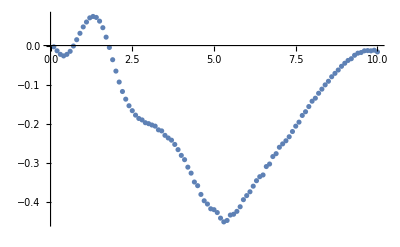

```mathematica
ListPlot[Transpose[{%[[All,1]],Re[%[[All,2,3]]]}]]
```

```mathematica
ParallelTable[{k,v2HZ[k,0.5,1.0,1.0]},{k,0.1,10,0.1}]
```

```mathematica
ParallelTable[{k,v2HZ[k,0.2,1.0,1.0]},{k,0.1,10,0.1}]
```

```mathematica
(*MonteCarlos*)
ParallelTable[{k,v2HZ[k,2.0,1.0,1.0]},{k,0.1,10,0.1}]
```

0.1 starts to run on kern 50

0.3 starts to run on kern 49

0.5 starts to run on kern 48

0.7 starts to run on kern 47

0.9 starts to run on kern 46

1.1 starts to run on kern 45

1.3 starts to run on kern 44

1.5 starts to run on kern 43

1.7 starts to run on kern 42

1.9 starts to run on kern 41

2.1 starts to run on kern 40

2.3 starts to run on kern 39

2.5 starts to run on kern 38

2.7 starts to run on kern 37

2.9 starts to run on kern 36

3.1 starts to run on kern 35

3.3 starts to run on kern 34

3.5 starts to run on kern 33

3.7 starts to run on kern 32

3.9 starts to run on kern 31

4.1 starts to run on kern 30

4.3 starts to run on kern 29

4.5 starts to run on kern 28

4.7 starts to run on kern 27

4.9 starts to run on kern 26

5.1 starts to run on kern 25

5.3 starts to run on kern 24

5.5 starts to run on kern 23

5.7 starts to run on kern 22

5.9 starts to run on kern 21

6.1 starts to run on kern 20

6.3 starts to run on kern 19

6.5 starts to run on kern 18

6.7 starts to run on kern 17

6.9 starts to run on kern 16

7.1 starts to run on kern 15

7.3 starts to run on kern 14

7.5 starts to run on kern 13

7.7 starts to run on kern 12

7.9 starts to run on kern 11

8.1 starts to run on kern 10

8.3 starts to run on kern 9

8.5 starts to run on kern 8

8.7 starts to run on kern 7

8.9 starts to run on kern 6

9.1 starts to run on kern 5

9.3 starts to run on kern 4

9.5 starts to run on kern 3

9.7 starts to run on kern 2

9.9 starts to run on kern 1

NIntegrate::maxp: The integral failed to converge after 50100 integrand evaluations. NIntegrate obtained -0.0431093+0. ⅈ and 0.00924806 for the integral and error estimates.

0.3 finishes num on kern 49

NIntegrate::maxp: The integral failed to converge after 50100 integrand evaluations. NIntegrate obtained 0.0193767+0. ⅈ and 0.078804 for the integral and error estimates.

0.1 finishes num on kern 50

NIntegrate::maxp: The integral failed to converge after 50100 integrand evaluations. NIntegrate obtained -0.0235125+0. ⅈ and 0.00357182 for the integral and error estimates.

0.5 finishes num on kern 48

Main calculation is done on kern 49 with k_T=0.3

0.4 starts to run on kern 49

NIntegrate::maxp: The integral failed to converge after 50100 integrand evaluations. NIntegrate obtained 0.000299+0. ⅈ and 0.0018827 for the integral and error estimates.

0.7 finishes num on kern 47

NIntegrate::maxp: The integral failed to converge after 50100 integrand evaluations. NIntegrate obtained 0.00900858+0. ⅈ and 0.00112946 for the integral and error estimates.

0.9 finishes num on kern 46

Main calculation is done on kern 50 with k_T=0.1

0.2 starts to run on kern 50

NIntegrate::maxp: The integral failed to converge after 50100 integrand evaluations. NIntegrate obtained 0.0117775+0. ⅈ and 0.000722861 for the integral and error estimates.

1.1 finishes num on kern 45

NIntegrate::maxp: The integral failed to converge after 50100 integrand evaluations. NIntegrate obtained 0.00576707+0. ⅈ and 0.000347281 for the integral and error estimates.

1.5 finishes num on kern 43

NIntegrate::maxp: The integral failed to converge after 50100 integrand evaluations. NIntegrate obtained 0.00950883+0. ⅈ and 0.000485247 for the integral and error estimates.

1.3 finishes num on kern 44

Main calculation is done on kern 48 with k_T=0.5

0.6 starts to run on kern 48

NIntegrate::maxp: The integral failed to converge after 50100 integrand evaluations. NIntegrate obtained 0.00141918+0. ⅈ and 0.000263651 for the integral and error estimates.

1.7 finishes num on kern 42

NIntegrate::maxp: The integral failed to converge after 50100 integrand evaluations. NIntegrate obtained -0.00227938+0. ⅈ and 0.000213673 for the integral and error estimates.

1.9 finishes num on kern 41

Main calculation is done on kern 46 with k_T=0.9

1. starts to run on kern 46

Main calculation is done on kern 47 with k_T=0.7

0.8 starts to run on kern 47

Main calculation is done on kern 43 with k_T=1.5

1.6 starts to run on kern 43

Main calculation is done on kern 45 with k_T=1.1

1.2 starts to run on kern 45

NIntegrate::maxp: The integral failed to converge after 50100 integrand evaluations. NIntegrate obtained -0.00467258+0. ⅈ and 0.000183415 for the integral and error estimates.

2.1 finishes num on kern 40

NIntegrate::maxp: The integral failed to converge after 50100 integrand evaluations. NIntegrate obtained -0.00611573+0. ⅈ and 0.000162942 for the integral and error estimates.

2.3 finishes num on kern 39

Main calculation is done on kern 44 with k_T=1.3

1.4 starts to run on kern 44

NIntegrate::maxp: The integral failed to converge after 50100 integrand evaluations. NIntegrate obtained -0.0066764+0. ⅈ and 0.000146113 for the integral and error estimates.

2.5 finishes num on kern 38

NIntegrate::maxp: The integral failed to converge after 50100 integrand evaluations. NIntegrate obtained -0.00677421+0. ⅈ and 0.000124004 for the integral and error estimates.

2.9 finishes num on kern 36

Main calculation is done on kern 42 with k_T=1.7

1.8 starts to run on kern 42

NIntegrate::maxp: The integral failed to converge after 50100 integrand evaluations. NIntegrate obtained -0.00677917+0. ⅈ and 0.00013411 for the integral and error estimates.

2.7 finishes num on kern 37

NIntegrate::maxp: The integral failed to converge after 50100 integrand evaluations. NIntegrate obtained -0.00562827+0. ⅈ and 0.000101105 for the integral and error estimates.

3.3 finishes num on kern 34

NIntegrate::maxp: The integral failed to converge after 50100 integrand evaluations. NIntegrate obtained -0.00529031+0. ⅈ and 0.0000894244 for the integral and error estimates.

3.5 finishes num on kern 33

Main calculation is done on kern 41 with k_T=1.9

2. starts to run on kern 41

NIntegrate::maxp: The integral failed to converge after 50100 integrand evaluations. NIntegrate obtained -0.00360059+0. ⅈ and 0.0000452072 for the integral and error estimates.

4.3 finishes num on kern 29

NIntegrate::maxp: The integral failed to converge after 50100 integrand evaluations. NIntegrate obtained -0.00478779+0. ⅈ and 0.0000764682 for the integral and error estimates.

3.7 finishes num on kern 32

Main calculation is done on kern 40 with k_T=2.1

2.2 starts to run on kern 40

NIntegrate::maxp: The integral failed to converge after 50100 integrand evaluations. NIntegrate obtained -0.00438884+0. ⅈ and 0.0000649923 for the integral and error estimates.

3.9 finishes num on kern 31

NIntegrate::maxp: The integral failed to converge after 50100 integrand evaluations. NIntegrate obtained -0.00408982+0. ⅈ and 0.0000542761 for the integral and error estimates.

4.1 finishes num on kern 30

Main calculation is done on kern 39 with k_T=2.3

2.4 starts to run on kern 39

Main calculation is done on kern 38 with k_T=2.5

2.6 starts to run on kern 38

Main calculation is done on kern 36 with k_T=2.9

3. starts to run on kern 36

NIntegrate::maxp: The integral failed to converge after 50100 integrand evaluations. NIntegrate obtained -0.00613327+0. ⅈ and 0.000112943 for the integral and error estimates.

3.1 finishes num on kern 35

NIntegrate::maxp: The integral failed to converge after 50100 integrand evaluations. NIntegrate obtained -0.00310878+0. ⅈ and 0.0000370727 for the integral and error estimates.

4.5 finishes num on kern 28

Main calculation is done on kern 34 with k_T=3.3

3.4 starts to run on kern 34

Main calculation is done on kern 37 with k_T=2.7

2.8 starts to run on kern 37

NIntegrate::maxp: The integral failed to converge after 50100 integrand evaluations. NIntegrate obtained -0.00272962+0. ⅈ and 0.0000306659 for the integral and error estimates.

4.7 finishes num on kern 27

Main calculation is done on kern 33 with k_T=3.5

3.6 starts to run on kern 33

Main calculation is done on kern 32 with k_T=3.7

3.8 starts to run on kern 32

Main calculation is done on kern 31 with k_T=3.9

4. starts to run on kern 31

Main calculation is done on kern 29 with k_T=4.3

4.4 starts to run on kern 29

NIntegrate::maxp: The integral failed to converge after 50100 integrand evaluations. NIntegrate obtained -0.0022792+0. ⅈ and 0.0000253133 for the integral and error estimates.

4.9 finishes num on kern 26

Main calculation is done on kern 30 with k_T=4.1

4.2 starts to run on kern 30

Main calculation is done on kern 35 with k_T=3.1

3.2 starts to run on kern 35

Main calculation is done on kern 28 with k_T=4.5

4.6 starts to run on kern 28

NIntegrate::maxp: The integral failed to converge after 50100 integrand evaluations. NIntegrate obtained -0.00195081+0. ⅈ and 0.0000212451 for the integral and error estimates.

5.1 finishes num on kern 25

Main calculation is done on kern 27 with k_T=4.7

4.8 starts to run on kern 27

NIntegrate::maxp: The integral failed to converge after 50100 integrand evaluations. NIntegrate obtained -0.00160444+0. ⅈ and 0.0000176353 for the integral and error estimates.

5.3 finishes num on kern 24

NIntegrate::maxp: The integral failed to converge after 50100 integrand evaluations. NIntegrate obtained -0.00124983+0. ⅈ and 0.000014616 for the integral and error estimates.

5.5 finishes num on kern 23

Main calculation is done on kern 26 with k_T=4.9

5. starts to run on kern 26

NIntegrate::maxp: The integral failed to converge after 50100 integrand evaluations. NIntegrate obtained -0.00101569+0. ⅈ and 0.0000123433 for the integral and error estimates.

5.7 finishes num on kern 22

NIntegrate::maxp: The integral failed to converge after 50100 integrand evaluations. NIntegrate obtained -0.000792464+0. ⅈ and 0.0000102887 for the integral and error estimates.

5.9 finishes num on kern 21

Main calculation is done on kern 25 with k_T=5.1

5.2 starts to run on kern 25

Main calculation is done on kern 24 with k_T=5.3

5.4 starts to run on kern 24

NIntegrate::maxp: The integral failed to converge after 50100 integrand evaluations. NIntegrate obtained -0.000626204+0. ⅈ and 8.75173×10^-6 for the integral and error estimates.

6.1 finishes num on kern 20

NIntegrate::maxp: The integral failed to converge after 50100 integrand evaluations. NIntegrate obtained -0.000494134+0. ⅈ and 7.39732×10^-6 for the integral and error estimates.

6.3 finishes num on kern 19

Main calculation is done on kern 23 with k_T=5.5

5.6 starts to run on kern 23

NIntegrate::maxp: The integral failed to converge after 50100 integrand evaluations. NIntegrate obtained -0.00038393+0. ⅈ and 6.24711×10^-6 for the integral and error estimates.

6.5 finishes num on kern 18

NIntegrate::maxp: The integral failed to converge after 50100 integrand evaluations. NIntegrate obtained -0.0410288+0. ⅈ and 0.00541526 for the integral and error estimates.

0.4 finishes num on kern 49

NIntegrate::maxp: The integral failed to converge after 50100 integrand evaluations. NIntegrate obtained -0.0497596+0. ⅈ and 0.020264 for the integral and error estimates.

0.2 finishes num on kern 50

Main calculation is done on kern 22 with k_T=5.7

5.8 starts to run on kern 22

Main calculation is done on kern 49 with k_T=0.4

Main calculation is done on kern 50 with k_T=0.2

NIntegrate::maxp: The integral failed to converge after 50100 integrand evaluations. NIntegrate obtained -0.000319027+0. ⅈ and 5.36049×10^-6 for the integral and error estimates.

6.7 finishes num on kern 17

Main calculation is done on kern 21 with k_T=5.9

6. starts to run on kern 21

NIntegrate::maxp: The integral failed to converge after 50100 integrand evaluations. NIntegrate obtained -0.00801521+0. ⅈ and 0.0025292 for the integral and error estimates.

0.6 finishes num on kern 48

NIntegrate::maxp: The integral failed to converge after 50100 integrand evaluations. NIntegrate obtained 0.0111496+0. ⅈ and 0.00089874 for the integral and error estimates.

1. finishes num on kern 46

Main calculation is done on kern 20 with k_T=6.1

6.2 starts to run on kern 20

NIntegrate::maxp: The integral failed to converge after 50100 integrand evaluations. NIntegrate obtained 0.00647569+0. ⅈ and 0.00145481 for the integral and error estimates.

0.8 finishes num on kern 47

NIntegrate::maxp: The integral failed to converge after 50100 integrand evaluations. NIntegrate obtained -0.000252039+0. ⅈ and 4.58672×10^-6 for the integral and error estimates.

6.9 finishes num on kern 16

NIntegrate::maxp: The integral failed to converge after 50100 integrand evaluations. NIntegrate obtained 0.0111754+0. ⅈ and 0.000588213 for the integral and error estimates.

1.2 finishes num on kern 45

NIntegrate::maxp: The integral failed to converge after 50100 integrand evaluations. NIntegrate obtained 0.00339214+0. ⅈ and 0.000299641 for the integral and error estimates.

1.6 finishes num on kern 43

Main calculation is done on kern 48 with k_T=0.6

NIntegrate::maxp: The integral failed to converge after 50100 integrand evaluations. NIntegrate obtained 0.00804437+0. ⅈ and 0.000408482 for the integral and error estimates.

1.4 finishes num on kern 44

NIntegrate::maxp: The integral failed to converge after 50100 integrand evaluations. NIntegrate obtained -0.000195766+0. ⅈ and 3.9251×10^-6 for the integral and error estimates.

7.1 finishes num on kern 15

Main calculation is done on kern 46 with k_T=1.

Main calculation is done on kern 45 with k_T=1.2

Main calculation is done on kern 43 with k_T=1.6

NIntegrate::maxp: The integral failed to converge after 50100 integrand evaluations. NIntegrate obtained -0.000151811+0. ⅈ and 3.34022×10^-6 for the integral and error estimates.

7.3 finishes num on kern 14

Main calculation is done on kern 47 with k_T=0.8

Main calculation is done on kern 19 with k_T=6.3

6.4 starts to run on kern 19

Main calculation is done on kern 44 with k_T=1.4

NIntegrate::maxp: The integral failed to converge after 50100 integrand evaluations. NIntegrate obtained -0.000266956+0. ⅈ and 0.000236254 for the integral and error estimates.

1.8 finishes num on kern 42

NIntegrate::maxp: The integral failed to converge after 50100 integrand evaluations. NIntegrate obtained -0.000120864+0. ⅈ and 2.94041×10^-6 for the integral and error estimates.

7.5 finishes num on kern 13

NIntegrate::maxp: The integral failed to converge after 50100 integrand evaluations. NIntegrate obtained -0.00349355+0. ⅈ and 0.000196076 for the integral and error estimates.

2. finishes num on kern 41

Main calculation is done on kern 18 with k_T=6.5

6.6 starts to run on kern 18

NIntegrate::maxp: The integral failed to converge after 50100 integrand evaluations. NIntegrate obtained -0.00528632+0. ⅈ and 0.000171523 for the integral and error estimates.

2.2 finishes num on kern 40

Main calculation is done on kern 42 with k_T=1.8

NIntegrate::maxp: The integral failed to converge after 50100 integrand evaluations. NIntegrate obtained -0.00010054+0. ⅈ and 2.59958×10^-6 for the integral and error estimates.

7.7 finishes num on kern 12

NIntegrate::maxp: The integral failed to converge after 50100 integrand evaluations. NIntegrate obtained -0.00646178+0. ⅈ and 0.000153812 for the integral and error estimates.

2.4 finishes num on kern 39

NIntegrate::maxp: The integral failed to converge after 50100 integrand evaluations. NIntegrate obtained -0.00685461+0. ⅈ and 0.000139819 for the integral and error estimates.

2.6 finishes num on kern 38

NIntegrate::maxp: The integral failed to converge after 50100 integrand evaluations. NIntegrate obtained -0.00643624+0. ⅈ and 0.000118645 for the integral and error estimates.

3. finishes num on kern 36

Main calculation is done on kern 41 with k_T=2.

NIntegrate::maxp: The integral failed to converge after 50100 integrand evaluations. NIntegrate obtained -0.00703449+0. ⅈ and 0.000129909 for the integral and error estimates.

2.8 finishes num on kern 37

NIntegrate::maxp: The integral failed to converge after 50100 integrand evaluations. NIntegrate obtained -0.00538396+0. ⅈ and 0.0000950801 for the integral and error estimates.

3.4 finishes num on kern 34

NIntegrate::maxp: The integral failed to converge after 50100 integrand evaluations. NIntegrate obtained -0.0000603078+0. ⅈ and 2.06505×10^-6 for the integral and error estimates.

8.1 finishes num on kern 10

NIntegrate::maxp: The integral failed to converge after 50100 integrand evaluations. NIntegrate obtained -0.0000482643+0. ⅈ and 1.91242×10^-6 for the integral and error estimates.

Main calculation is done on kern 40 with k_T=2.2

8.3 finishes num on kern 9

NIntegrate::maxp: The integral failed to converge after 50100 integrand evaluations. NIntegrate obtained -0.00515279+0. ⅈ and 0.0000833286 for the integral and error estimates.

3.6 finishes num on kern 33

NIntegrate::maxp: The integral failed to converge after 50100 integrand evaluations. NIntegrate obtained -0.0000748166+0. ⅈ and 2.30324×10^-6 for the integral and error estimates.

7.9 finishes num on kern 11

Main calculation is done on kern 17 with k_T=6.7

6.8 starts to run on kern 17

Main calculation is done on kern 39 with k_T=2.4

Main calculation is done on kern 38 with k_T=2.6

Main calculation is done on kern 36 with k_T=3.

NIntegrate::maxp: The integral failed to converge after 50100 integrand evaluations. NIntegrate obtained -0.00457221+0. ⅈ and 0.0000705717 for the integral and error estimates.

3.8 finishes num on kern 32

Main calculation is done on kern 37 with k_T=2.8

NIntegrate::maxp: The integral failed to converge after 50100 integrand evaluations. NIntegrate obtained -0.00329948+0. ⅈ and 0.0000406293 for the integral and error estimates.

4.4 finishes num on kern 29

NIntegrate::maxp: The integral failed to converge after 50100 integrand evaluations. NIntegrate obtained -0.0000259608+0. ⅈ and 1.60148×10^-6 for the integral and error estimates.

8.7 finishes num on kern 7

Main calculation is done on kern 34 with k_T=3.4

NIntegrate::maxp: The integral failed to converge after 50100 integrand evaluations. NIntegrate obtained -0.0000177499+0. ⅈ and 1.50391×10^-6 for the integral and error estimates.

8.9 finishes num on kern 6

Main calculation is done on kern 16 with k_T=6.9

7. starts to run on kern 16

NIntegrate::maxp: The integral failed to converge after 50100 integrand evaluations. NIntegrate obtained -0.00418582+0. ⅈ and 0.000059274 for the integral and error estimates.

4. finishes num on kern 31

NIntegrate::maxp: The integral failed to converge after 50100 integrand evaluations. NIntegrate obtained -0.0000350907+0. ⅈ and 1.72898×10^-6 for the integral and error estimates.

8.5 finishes num on kern 8

Main calculation is done on kern 33 with k_T=3.6

NIntegrate::maxp: The integral failed to converge after 50100 integrand evaluations. NIntegrate obtained -5.03638×10^-6+0. ⅈ and 1.26443×10^-6 for the integral and error estimates.

9.5 finishes num on kern 3

Main calculation is done on kern 15 with k_T=7.1

7.2 starts to run on kern 15

NIntegrate::maxp: The integral failed to converge after 50100 integrand evaluations. NIntegrate obtained -0.0038097+0. ⅈ and 0.0000496876 for the integral and error estimates.

4.2 finishes num on kern 30

NIntegrate::maxp: The integral failed to converge after 50100 integrand evaluations. NIntegrate obtained -0.00602672+0. ⅈ and 0.000107732 for the integral and error estimates.

3.2 finishes num on kern 35

Main calculation is done on kern 32 with k_T=3.8

NIntegrate::maxp: The integral failed to converge after 50100 integrand evaluations. NIntegrate obtained -0.0000125351+0. ⅈ and 1.39468×10^-6 for the integral and error estimates.

9.1 finishes num on kern 5

Main calculation is done on kern 14 with k_T=7.3

7.4 starts to run on kern 14

Main calculation is done on kern 13 with k_T=7.5

7.6 starts to run on kern 13

NIntegrate::maxp: The integral failed to converge after 50100 integrand evaluations. NIntegrate obtained -3.90246×10^-6+0. ⅈ and 1.17835×10^-6 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 50100 integrand evaluations. NIntegrate obtained -7.71072×10^-6+0. ⅈ and 1.33238×10^-6 for the integral and error estimates.

9.7 finishes num on kern 2

9.3 finishes num on kern 4

Main calculation is done on kern 31 with k_T=4.

Main calculation is done on kern 29 with k_T=4.4

Main calculation is done on kern 12 with k_T=7.7

7.8 starts to run on kern 12

NIntegrate::maxp: The integral failed to converge after 50100 integrand evaluations. NIntegrate obtained -1.61757×10^-6+0. ⅈ and 1.07989×10^-6 for the integral and error estimates.

9.9 finishes num on kern 1

NIntegrate::maxp: The integral failed to converge after 50100 integrand evaluations. NIntegrate obtained -0.00292999+0. ⅈ and 0.0000339532 for the integral and error estimates.

4.6 finishes num on kern 28

Main calculation is done on kern 35 with k_T=3.2

Main calculation is done on kern 30 with k_T=4.2

Main calculation is done on kern 9 with k_T=8.3

8.4 starts to run on kern 9

Main calculation is done on kern 10 with k_T=8.1

8.2 starts to run on kern 10

NIntegrate::maxp: The integral failed to converge after 50100 integrand evaluations. NIntegrate obtained -0.00246892+0. ⅈ and 0.0000278418 for the integral and error estimates.

4.8 finishes num on kern 27

Main calculation is done on kern 7 with k_T=8.7

8.8 starts to run on kern 7

Main calculation is done on kern 11 with k_T=7.9

8. starts to run on kern 11

Main calculation is done on kern 6 with k_T=8.9

9. starts to run on kern 6

Main calculation is done on kern 8 with k_T=8.5

8.6 starts to run on kern 8

Main calculation is done on kern 3 with k_T=9.5

9.6 starts to run on kern 3

Main calculation is done on kern 28 with k_T=4.6

Main calculation is done on kern 5 with k_T=9.1

9.2 starts to run on kern 5

Main calculation is done on kern 4 with k_T=9.3

9.4 starts to run on kern 4

Main calculation is done on kern 2 with k_T=9.7

9.8 starts to run on kern 2

Main calculation is done on kern 1 with k_T=9.9

10. starts to run on kern 1

NIntegrate::maxp: The integral failed to converge after 50100 integrand evaluations. NIntegrate obtained -0.00210434+0. ⅈ and 0.0000230316 for the integral and error estimates.

5. finishes num on kern 26

Main calculation is done on kern 27 with k_T=4.8

NIntegrate::maxp: The integral failed to converge after 50100 integrand evaluations. NIntegrate obtained -0.00172721+0. ⅈ and 0.0000191955 for the integral and error estimates.

5.2 finishes num on kern 25

Main calculation is done on kern 26 with k_T=5.

NIntegrate::maxp: The integral failed to converge after 50100 integrand evaluations. NIntegrate obtained -0.00139337+0. ⅈ and 0.0000159813 for the integral and error estimates.

5.4 finishes num on kern 24

Main calculation is done on kern 25 with k_T=5.2

NIntegrate::maxp: The integral failed to converge after 50100 integrand evaluations. NIntegrate obtained -0.00113878+0. ⅈ and 0.0000133991 for the integral and error estimates.

5.6 finishes num on kern 23

Main calculation is done on kern 24 with k_T=5.4

NIntegrate::maxp: The integral failed to converge after 50100 integrand evaluations. NIntegrate obtained -0.000903523+0. ⅈ and 0.0000113264 for the integral and error estimates.

5.8 finishes num on kern 22

NIntegrate::maxp: The integral failed to converge after 50100 integrand evaluations. NIntegrate obtained -0.000697745+0. ⅈ and 9.43764×10^-6 for the integral and error estimates.

6. finishes num on kern 21

Main calculation is done on kern 23 with k_T=5.6

NIntegrate::maxp: The integral failed to converge after 50100 integrand evaluations. NIntegrate obtained -0.000545531+0. ⅈ and 7.9887×10^-6 for the integral and error estimates.

6.2 finishes num on kern 20

Main calculation is done on kern 22 with k_T=5.8

NIntegrate::maxp: The integral failed to converge after 50100 integrand evaluations. NIntegrate obtained -0.000435128+0. ⅈ and 6.78757×10^-6 for the integral and error estimates.

6.4 finishes num on kern 19

Main calculation is done on kern 21 with k_T=6.

NIntegrate::maxp: The integral failed to converge after 50100 integrand evaluations. NIntegrate obtained -0.000343224+0. ⅈ and 5.75236×10^-6 for the integral and error estimates.

6.6 finishes num on kern 18

Main calculation is done on kern 20 with k_T=6.2

NIntegrate::maxp: The integral failed to converge after 50100 integrand evaluations. NIntegrate obtained -0.000276704+0. ⅈ and 4.93152×10^-6 for the integral and error estimates.

6.8 finishes num on kern 17

Main calculation is done on kern 19 with k_T=6.4

Main calculation is done on kern 18 with k_T=6.6

NIntegrate::maxp: The integral failed to converge after 50100 integrand evaluations. NIntegrate obtained -0.000217532+0. ⅈ and 4.2111×10^-6 for the integral and error estimates.

7. finishes num on kern 16

NIntegrate::maxp: The integral failed to converge after 50100 integrand evaluations. NIntegrate obtained -0.000175794+0. ⅈ and 3.66371×10^-6 for the integral and error estimates.

7.2 finishes num on kern 15

NIntegrate::maxp: The integral failed to converge after 50100 integrand evaluations. NIntegrate obtained -0.000139146+0. ⅈ and 3.17008×10^-6 for the integral and error estimates.

7.4 finishes num on kern 14

Main calculation is done on kern 17 with k_T=6.8

NIntegrate::maxp: The integral failed to converge after 50100 integrand evaluations. NIntegrate obtained -0.000108399+0. ⅈ and 2.74329×10^-6 for the integral and error estimates.

7.6 finishes num on kern 13

NIntegrate::maxp: The integral failed to converge after 50100 integrand evaluations. NIntegrate obtained -0.0000916455+0. ⅈ and 2.45824×10^-6 for the integral and error estimates.

7.8 finishes num on kern 12

Main calculation is done on kern 16 with k_T=7.

NIntegrate::maxp: The integral failed to converge after 50100 integrand evaluations. NIntegrate obtained -0.000054667+0. ⅈ and 1.97577×10^-6 for the integral and error estimates.

8.2 finishes num on kern 10

Main calculation is done on kern 15 with k_T=7.2

NIntegrate::maxp: The integral failed to converge after 50100 integrand evaluations. NIntegrate obtained -0.0000420314+0. ⅈ and 1.80706×10^-6 for the integral and error estimates.

8.4 finishes num on kern 9

NIntegrate::maxp: The integral failed to converge after 50100 integrand evaluations. NIntegrate obtained -0.0000710551+0. ⅈ and 2.18517×10^-6 for the integral and error estimates.

8. finishes num on kern 11

NIntegrate::maxp: The integral failed to converge after 50100 integrand evaluations. NIntegrate obtained -0.0000199399+0. ⅈ and 1.53133×10^-6 for the integral and error estimates.

8.8 finishes num on kern 7

Main calculation is done on kern 14 with k_T=7.4

Main calculation is done on kern 13 with k_T=7.6

NIntegrate::maxp: The integral failed to converge after 50100 integrand evaluations. NIntegrate obtained -0.0000304911+0. ⅈ and 1.65412×10^-6 for the integral and error estimates.

8.6 finishes num on kern 8

NIntegrate::maxp: The integral failed to converge after 50100 integrand evaluations. NIntegrate obtained -0.0000133854+0. ⅈ and 1.44792×10^-6 for the integral and error estimates.

9. finishes num on kern 6

Main calculation is done on kern 12 with k_T=7.8

NIntegrate::maxp: The integral failed to converge after 50100 integrand evaluations. NIntegrate obtained -9.57391×10^-6+0. ⅈ and 1.37835×10^-6 for the integral and error estimates.

9.2 finishes num on kern 5

NIntegrate::maxp: The integral failed to converge after 50100 integrand evaluations. NIntegrate obtained -5.48769×10^-6+0. ⅈ and 1.2093×10^-6 for the integral and error estimates.

9.6 finishes num on kern 3

Main calculation is done on kern 10 with k_T=8.2

NIntegrate::maxp: The integral failed to converge after 50100 integrand evaluations. NIntegrate obtained -2.70446×10^-6+0. ⅈ and 1.13914×10^-6 for the integral and error estimates.

9.8 finishes num on kern 2

Main calculation is done on kern 9 with k_T=8.4

NIntegrate::maxp: The integral failed to converge after 50100 integrand evaluations. NIntegrate obtained -6.00608×10^-6+0. ⅈ and 1.29892×10^-6 for the integral and error estimates.

9.4 finishes num on kern 4

Main calculation is done on kern 7 with k_T=8.8

Main calculation is done on kern 11 with k_T=8.

NIntegrate::maxp: The integral failed to converge after 50100 integrand evaluations. NIntegrate obtained -4.45558×10^-6+0. ⅈ and 1.04752×10^-6 for the integral and error estimates.

10. finishes num on kern 1

Main calculation is done on kern 8 with k_T=8.6

Main calculation is done on kern 6 with k_T=9.

Main calculation is done on kern 5 with k_T=9.2

Main calculation is done on kern 3 with k_T=9.6

Main calculation is done on kern 2 with k_T=9.8

Main calculation is done on kern 4 with k_T=9.4

Main calculation is done on kern 1 with k_T=10.

{{0.1,{0.0193767,19.7853,0.000979347}},{0.2,{-0.0497596+0. ⅈ,5.14103,-0.00967893+0. ⅈ}},{0.3,{-0.0431093+0. ⅈ,2.37059,-0.018185+0. ⅈ}},{0.4,{-0.0410288+0. ⅈ,1.40039,-0.0292981+0. ⅈ}},{0.5,{-0.0235125+0. ⅈ,0.923367,-0.0254638+0. ⅈ}},{0.6,{-0.00801521+0. ⅈ,0.64749,-0.0123789+0. ⅈ}},{0.7,{0.000299,0.500544,0.00059735}},{0.8,{0.00647569,0.38877,0.0166569}},{0.9,{0.00900858,0.298778,0.0301515}},{1.,{0.0111496,0.244728,0.045559}},{1.1,{0.0117775,0.198251,0.0594068}},{1.2,{0.0111754,0.155247,0.0719843}},{1.3,{0.00950883,0.129997,0.0731467}},{1.4,{0.00804437,0.109293,0.0736035}},{1.5,{0.00576707,0.0919185,0.0627411}},{1.6,{0.00339214,0.080468,0.0421552}},{1.7,{0.00141918,0.0694774,0.0204264}},{1.8,{-0.000266956+0. ⅈ,0.0634968,-0.00420424+0. ⅈ}},{1.9,{-0.00227938+0. ⅈ,0.0569149,-0.0400489+0. ⅈ}},{2.,{-0.00349355+0. ⅈ,0.0534443,-0.0653681+0. ⅈ}},{2.1,{-0.00467258+0. ⅈ,0.0510484,-0.0915323+0. ⅈ}},{2.2,{-0.00528632+0. ⅈ,0.0466081,-0.113421+0. ⅈ}},{2.3,{-0.00611573+0. ⅈ,0.0447654,-0.136617+0. ⅈ}},{2.4,{-0.00646178+0. ⅈ,0.0421233,-0.153402+0. ⅈ}},{2.5,{-0.0066764+0. ⅈ,0.0397446,-0.167983+0. ⅈ}},{2.6,{-0.00685461+0. ⅈ,0.0384855,-0.178109+0. ⅈ}},{2.7,{-0.00677917+0. ⅈ,0.0372226,-0.182125+0. ⅈ}},{2.8,{-0.00703449+0. ⅈ,0.0351532,-0.200109+0. ⅈ}},{2.9,{-0.00677421+0. ⅈ,0.0345175,-0.196254+0. ⅈ}},{3.,{-0.00643624+0. ⅈ,0.0323013,-0.199256+0. ⅈ}},{3.1,{-0.00613327+0. ⅈ,0.030558,-0.200709+0. ⅈ}},{3.2,{-0.00602672+0. ⅈ,0.0282545,-0.213301+0. ⅈ}},{3.3,{-0.00562827+0. ⅈ,0.0268886,-0.209318+0. ⅈ}},{3.4,{-0.00538396+0. ⅈ,0.0252735,-0.213028+0. ⅈ}},{3.5,{-0.00529031+0. ⅈ,0.0233068,-0.226986+0. ⅈ}},{3.6,{-0.00515279+0. ⅈ,0.0212472,-0.242516+0. ⅈ}},{3.7,{-0.00478779+0. ⅈ,0.019655,-0.243592+0. ⅈ}},{3.8,{-0.00457221+0. ⅈ,0.0180796,-0.252894+0. ⅈ}},{3.9,{-0.00438884+0. ⅈ,0.0164961,-0.266053+0. ⅈ}},{4.,{-0.00418582+0. ⅈ,0.0150862,-0.27746+0. ⅈ}},{4.1,{-0.00408982+0. ⅈ,0.0133028,-0.30744+0. ⅈ}},{4.2,{-0.0038097+0. ⅈ,0.0118653,-0.321078+0. ⅈ}},{4.3,{-0.00360059+0. ⅈ,0.0108249,-0.332622+0. ⅈ}},{4.4,{-0.00329948+0. ⅈ,0.00962919,-0.342654+0. ⅈ}},{4.5,{-0.00310878+0. ⅈ,0.00872964,-0.356118+0. ⅈ}},{4.6,{-0.00292999+0. ⅈ,0.00772015,-0.379525+0. ⅈ}},{4.7,{-0.00272962+0. ⅈ,0.00686939,-0.39736+0. ⅈ}},{4.8,{-0.00246892+0. ⅈ,0.00619371,-0.398618+0. ⅈ}},{4.9,{-0.0022792+0. ⅈ,0.00544686,-0.418442+0. ⅈ}},{5.,{-0.00210434+0. ⅈ,0.00496618,-0.423735+0. ⅈ}},{5.1,{-0.00195081+0. ⅈ,0.00438435,-0.444949+0. ⅈ}},{5.2,{-0.00172721+0. ⅈ,0.00391699,-0.440955+0. ⅈ}},{5.3,{-0.00160444+0. ⅈ,0.00358047,-0.448108+0. ⅈ}},{5.4,{-0.00139337+0. ⅈ,0.00318278,-0.437784+0. ⅈ}},{5.5,{-0.00124983+0. ⅈ,0.00287868,-0.434169+0. ⅈ}},{5.6,{-0.00113878+0. ⅈ,0.00262818,-0.433295+0. ⅈ}},{5.7,{-0.00101569+0. ⅈ,0.00236615,-0.429259+0. ⅈ}},{5.8,{-0.000903523+0. ⅈ,0.00218552,-0.413413+0. ⅈ}},{5.9,{-0.000792464+0. ⅈ,0.00197737,-0.400766+0. ⅈ}},{6.,{-0.000697745+0. ⅈ,0.00178901,-0.390017+0. ⅈ}},{6.1,{-0.000626204+0. ⅈ,0.00165465,-0.378451+0. ⅈ}},{6.2,{-0.000545531+0. ⅈ,0.00153488,-0.355424+0. ⅈ}},{6.3,{-0.000494134+0. ⅈ,0.00141367,-0.349541+0. ⅈ}},{6.4,{-0.000435128+0. ⅈ,0.00130805,-0.332654+0. ⅈ}},{6.5,{-0.00038393+0. ⅈ,0.00119979,-0.319998+0. ⅈ}},{6.6,{-0.000343224+0. ⅈ,0.00110226,-0.311381+0. ⅈ}},{6.7,{-0.000319027+0. ⅈ,0.00102759,-0.31046+0. ⅈ}},{6.8,{-0.000276704+0. ⅈ,0.000939111,-0.294645+0. ⅈ}},{6.9,{-0.000252039+0. ⅈ,0.000876916,-0.287416+0. ⅈ}},{7.,{-0.000217532+0. ⅈ,0.00080563,-0.270015+0. ⅈ}},{7.1,{-0.000195766+0. ⅈ,0.000771814,-0.253645+0. ⅈ}},{7.2,{-0.000175794+0. ⅈ,0.000721795,-0.243551+0. ⅈ}},{7.3,{-0.000151811+0. ⅈ,0.000685101,-0.221589+0. ⅈ}},{7.4,{-0.000139146+0. ⅈ,0.000638215,-0.218024+0. ⅈ}},{7.5,{-0.000120864+0. ⅈ,0.000610169,-0.198082+0. ⅈ}},{7.6,{-0.000108399+0. ⅈ,0.000568835,-0.190563+0. ⅈ}},{7.7,{-0.00010054+0. ⅈ,0.000539549,-0.186341+0. ⅈ}},{7.8,{-0.0000916455+0. ⅈ,0.000511264,-0.179253+0. ⅈ}},{7.9,{-0.0000748166+0. ⅈ,0.000503684,-0.148539+0. ⅈ}},{8.,{-0.0000710551+0. ⅈ,0.000478847,-0.148388+0. ⅈ}},{8.1,{-0.0000603078+0. ⅈ,0.000461368,-0.130715+0. ⅈ}},{8.2,{-0.000054667+0. ⅈ,0.000444492,-0.122987+0. ⅈ}},{8.3,{-0.0000482643+0. ⅈ,0.000434681,-0.111034+0. ⅈ}},{8.4,{-0.0000420314+0. ⅈ,0.000418533,-0.100426+0. ⅈ}},{8.5,{-0.0000350907+0. ⅈ,0.000399547,-0.0878264+0. ⅈ}},{8.6,{-0.0000304911+0. ⅈ,0.000395828,-0.0770312+0. ⅈ}},{8.7,{-0.0000259608+0. ⅈ,0.000380089,-0.0683018+0. ⅈ}},{8.8,{-0.0000199399+0. ⅈ,0.000370739,-0.0537842+0. ⅈ}},{8.9,{-0.0000177499+0. ⅈ,0.00035906,-0.0494343+0. ⅈ}},{9.,{-0.0000133854+0. ⅈ,0.000353006,-0.0379185+0. ⅈ}},{9.1,{-0.0000125351+0. ⅈ,0.000346034,-0.036225+0. ⅈ}},{9.2,{-9.57391×10^-6+0. ⅈ,0.00033376,-0.028685+0. ⅈ}},{9.3,{-7.71072×10^-6+0. ⅈ,0.000320118,-0.0240871+0. ⅈ}},{9.4,{-6.00608×10^-6+0. ⅈ,0.000314145,-0.0191188+0. ⅈ}},{9.5,{-5.03638×10^-6+0. ⅈ,0.000300881,-0.0167388+0. ⅈ}},{9.6,{-5.48769×10^-6+0. ⅈ,0.000297138,-0.0184685+0. ⅈ}},{9.7,{-3.90246×10^-6+0. ⅈ,0.000285891,-0.0136502+0. ⅈ}},{9.8,{-2.70446×10^-6+0. ⅈ,0.000273171,-0.00990024+0. ⅈ}},{9.9,{-1.61757×10^-6+0. ⅈ,0.000268954,-0.00601431+0. ⅈ}},{10.,{-4.45558×10^-6+0. ⅈ,0.000251404,-0.0177228+0. ⅈ}}}

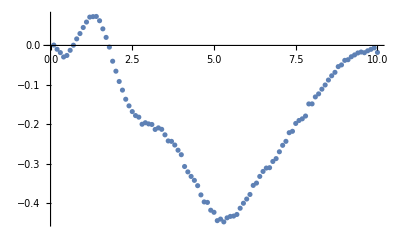

```mathematica
ListPlot[Transpose[{%[[All,1]],Re[%[[All,2,3]]]}]]
```

```mathematica
Getv2kT[b_,rA_,rB_]:=Module[{v2kTb05,i,kT,x1u,x3u,bu,ti},
ti=AbsoluteTime[];
v2kTb05=ParallelTable[{kT,v2HZ[kT,b,rA,rB]},{kT,0.2,10,0.2}];
Print[ListPlot[{Transpose[{v2kTb05[[All,1]],Re[v2kTb05[[All,2,3]]]}]},PlotStyle->{Red,Blue}]];
Print["Computatino time: ", AbsoluteTime[]-ti];
v2kTb05
]
```

```mathematica
LaunchKernels[50];
$KernelCount
```

50

```mathematica
(*CloseKernels[]*)
```

```mathematica
Getv2kT[2.0,1.0,1.0]
```

0.2 starts to run on kern 189

0.4 starts to run on kern 188

0.6 starts to run on kern 187

0.8 starts to run on kern 186

1. starts to run on kern 185

1.2 starts to run on kern 184

1.4 starts to run on kern 183

1.6 starts to run on kern 182

1.8 starts to run on kern 181

2. starts to run on kern 180

2.2 starts to run on kern 179

2.4 starts to run on kern 178

2.6 starts to run on kern 177

2.8 starts to run on kern 176

3. starts to run on kern 175

3.2 starts to run on kern 174

3.4 starts to run on kern 173

3.6 starts to run on kern 172

3.8 starts to run on kern 171

4. starts to run on kern 170

4.2 starts to run on kern 169

4.4 starts to run on kern 168

4.6 starts to run on kern 167

4.8 starts to run on kern 166

5. starts to run on kern 165

5.2 starts to run on kern 164

5.4 starts to run on kern 163

5.6 starts to run on kern 162

5.8 starts to run on kern 161

6. starts to run on kern 160

6.2 starts to run on kern 159

6.4 starts to run on kern 158

6.6 starts to run on kern 157

6.8 starts to run on kern 156

7. starts to run on kern 155

7.2 starts to run on kern 154

7.4 starts to run on kern 153

7.6 starts to run on kern 152

7.8 starts to run on kern 151

8. starts to run on kern 150

8.2 starts to run on kern 149

8.4 starts to run on kern 148

8.6 starts to run on kern 147

8.8 starts to run on kern 146

9. starts to run on kern 145

9.2 starts to run on kern 144

9.4 starts to run on kern 143

9.6 starts to run on kern 142

9.8 starts to run on kern 141

10. starts to run on kern 140